```mathematica
ClearAll["Global`*"]
$Assumptions=A∈Integers&&A>2&&α∈Reals&&α>0&&λ∈Reals&&λ>=0&&β∈Reals&&β>0&&R∈Reals&&Rp∈Reals;
```

system parameter:
A (int) : total number of particles
F (int) : number of fragments
Z (int array) : number of particles in fragments
d (int) : number of spatial dimensions (ECCE: do not use; from the 1-dim result, one should be able to deduce the d-dim variant)

```mathematica
spacedim=3;
A=3;
F=2;
Z={2,1};
If[Total[Z]!=A||Dimensions[Z][[1]]!=F,Print["System definition erroneous."]]
(* (B Subscript[(oson), 1] Subscript[B, 2]... Subscript[B, Subscript[Z, 1]])-(Subscript[B, 1]... Subscript[B, Subscript[Z, 1]]... Subscript[B, Subscript[Z, 1]+Subscript[Z, 2]]) *)
(*idPairs=Table[{n,n+Z[[1]]},{n,Z[[1]]}];*)
(* (B Subscript[(oson), 1] Subscript[B, 2]... Subscript[B, Subscript[Z, 1]])-(Subscript[B, 1] Subscript[B, 2].Subscript[B, Subscript[Z, 1]+Subscript[Z, 2]]) *)
(*idPairs={{1,Z[[1]]+1}};*)
idPairs={};

intPairs=Tuples[{Table[n,{n,Z[[1]]}],Table[n,{n,Z[[1]]+1,Z[[1]]+Z[[2]]}]}];
intBosePairs=Complement[intPairs,idPairs];
intTriples=Union[Tuples[{Table[n,{n,Z[[1]]}],Table[n,{n,Z[[1]]+1,Z[[1]]+Z[[2]]}],Table[n,{n,Z[[1]]+1,Z[[1]]+Z[[2]]}]}]//Select[#[[2]]≠#[[3]]&],Tuples[{Table[n,{n,Z[[1]]}],Table[n,{n,Z[[1]]}],Table[n,{n,Z[[1]]+1,Z[[1]]+Z[[2]]}]}]//Select[#[[1]]≠#[[2]]&]];
intBoseTriples={};
Do[
addtriple=True;
Do[
If[SubsetQ[tri,pai],addtriple=False,0]
,{pai,idPairs}];
If[addtriple,AppendTo[intBoseTriples,tri]];
,{tri,intTriples}];
intBoseTriples=DeleteDuplicates[Table[Sort[intBoseTriples[[n]]],{n,Length[intBoseTriples]}]];
Print["F_1 ⊕ F_2 = "<>ToString[Z[[1]]]<>" ⊕ "<>ToString[Z[[2]]]]
Print["∑_(ij ∈ Pairs) δ_ij  +  ∑_(ijk ∈ Triples) δ_ijδ_ik = "<>ToString[Length[intBosePairs]]<>"·δ_ij + "<>ToString[Length[intBoseTriples]]<>"·δ_ijδ_ik"]
Print["Pairs = ",intBosePairs,"   Triples = ",intBoseTriples]
intPart=Join[Table[AppendTo[intBosePairs[[n]],intBosePairs[[n]][[1]]],{n,Length[intBosePairs]}],intBoseTriples,{{1,1,1}}];
```

F_1 ⊕ F_2 = 2 ⊕ 1

∑_(ij ∈ Pairs) δ_ij  +  ∑_(ijk ∈ Triples) δ_ijδ_ik = 2·δ_ij + 1·δ_ijδ_ik

Pairs = {{1,3},{2,3}}   Triples = {{1,2,3}}

coordinate transformations:
single-particle   →  cluster-relative : T
cluster-relative  →  single-particle  : T^-1

```mathematica
SingleToCluster={};
For[f=1,f≤F,f++,{
For[i=1,i≤Z[[f]]-1,i++,{
AppendTo[SingleToCluster,
Table[Which[j<=Prepend[Accumulate[Z],0][[f]],0,j>Prepend[Accumulate[Z],0][[f+1]],0,j==Prepend[Accumulate[Z],0][[f]]+i,(Z[[f]]-1)/Z[[f]],1==1,-1/Z[[f]]],{j,1,A}]
]
}];
}];
For[f=1,f<F,f++,{
AppendTo[SingleToCluster,
Table[Which[j<=Prepend[Accumulate[Z],0][[f]],0,j>Prepend[Accumulate[Z],0][[f+2]],0,j<=Prepend[Accumulate[Z],0][[f+1]],1/Z[[f]],1==1,-1/Z[[f+1]]],{j,1,A}]
]
}];
AppendTo[SingleToCluster,
Table[1/A,{j,1,A}]
];
Single=Array[Subscript["r⃗", ##]&,{A}];
Cluster=Flatten[Table[Array[Subscript["r̄", Prepend[Accumulate[Z],0][[f]]+##]&,{Z[[f]]-1}],{f,F}]];
AppendTo[Cluster,ArrayFlatten[Array[Subscript["R⃗", ##]&,{F-1}],1][[1]]];AppendTo[Cluster,"(R⃗)_cm"];
Tmat=SingleToCluster;
Tmatinv=Inverse[SingleToCluster];
TproR=Table[If[(m==A-1),Tmat[[m,n]],0],{m,A},{n,A}];
Print[Cluster//MatrixForm,"=",SingleToCluster//MatrixForm,"·",Single//MatrixForm]
Print[Cluster//MatrixForm,"=",TproR//MatrixForm,"·",Single//MatrixForm]
```

((r̄)_1
(R⃗)_1
(R⃗)_cm)=(1/2 | -1/2 | 0
1/2 | 1/2 | -1
1/3 | 1/3 | 1/3)·((r⃗)_1
(r⃗)_2
(r⃗)_3)

((r̄)_1
(R⃗)_1
(R⃗)_cm)=(0 | 0 | 0
1/2 | 1/2 | -1
0 | 0 | 0)·((r⃗)_1
(r⃗)_2
(r⃗)_3)

quadratic form of fragment wave functions in cluster-relative coordinates:
ϕ_A ϕ_B=e^(-α_1(2 ∑_(j=1)^(A_1-1) r_j^2+∑_(j≠k)^(A_1-1) r_j r_k))·e^(1↔2)=∏_(i∈{1,2}) e^(-1/2(r_1,…,r_(A_i-1))(4 α_i
2 α_i
2 α_i2 α_i
4 α_i
2 α_i2 α_i
2 α_i
4 α_i) (r_1
⋮
r_(A_i-1)))
the matrix is set up row-wise
in the i-th row, the quadratic form of the j-th fragment is placed
with i-1 being the number of fragments with n<j which contain more than a single particle

```mathematica
Wmat={};
posInW=0;
For[f=1,f≤F,f++,(
If[Z[[f]]>1,
posInW+=1;
AppendTo[Wmat,Table[If[pos==posInW,Table[If[m==n,4 Subscript[a, f],2 Subscript[a, f]],{n,Z[[f]]-1},{m,Z[[f]]-1}],0],{pos,F}]];
];
)];
Wmat=Table[If[(m>A-2)||(n>A-2),0,ArrayFlatten[Wmat][[n]][[m]]],{n,A},{m,A}];
Print[Wmat//MatrixForm]
```

(4 α_1 | 0 | 0
0 | 0 | 0
0 | 0 | 0)

matrix representation of the permutation (single-particle coordinates):
(a | b | ... | A
p(a) | p(b) | ... | p(A))   original order
permuted order      ⇒    p(a)-th row→(⋮
a
⋮)=(□ | □ | □
□ | □ | □
□ | □ | □)·(a
⋮
A)
Pij[ i,j ] = Perm[ {{i,j},{j,i}} ]

```mathematica
Pij[i_,j_]:=Table[If[((r==i)&&(c==j))||((r==j)&&(c==i))||((r≠i)&&(c≠j)&&(c==r)),1,0],{r,1,A},{c,1,A}];
Perm[ord_]:=
Module[{},
pmat=IdentityMatrix[A];
Do[
pmat[[move[[1]],move[[1]]]]=0;
pmat[[move[[2]],move[[1]]]]=1;
,{move,ord}];
If[(Total[pmat,{1}]==ConstantArray[1,A])&&(Total[pmat,{2}]==ConstantArray[1,A]),
pmat,Print["illdefined permutation!"]]
];
interFragmentAntisymmetrizer=Flatten[Table[Join[DeleteDuplicates[Map[Sort,Select[Tuples[idPairs,n],DuplicateFreeQ[#]&]]],
Map[Reverse,DeleteDuplicates[Map[Sort,Select[Tuples[idPairs,n],DuplicateFreeQ[#]&]]],2],2
],{n,0,Length[idPairs]}],1];
Print["(Â)_AB = ",interFragmentAntisymmetrizer];
```

(Â)_AB = {{}}

quadratic form of a two-body Gaussian interaction in cluster-relative coordinates:
V_(F_1 F_2)=∑_((i∈F_1)_(j∈F_2)) e^(-(λ(r_i-r_j))^2)

```mathematica
Pv[i_,j_]:=Table[If[(n==m==j)||(n==m==i),1,0],{n,A},{m,A}];
Vr[i_,j_,λ_]:=If[i≠j,Table[Which[((n==m==i))||((n==m==(j))),2 λ,((n==i)&&(m==j))||((m==i)&&(n==j)),-2 λ,1==1,0],{n,A},{m,A}],Table[0,{n,A},{m,A}]];
Vij[i_,j_,λ_]:=Transpose[Pv[i,j].Tmatinv].Vr[i,j,λ].Pv[i,j].Tmatinv;
Vijk[i_,j_,k_,λ_]:=Transpose[Pv[i,j].Tmatinv].Vr[i,j,λ].Pv[i,j].Tmatinv+Transpose[Pv[i,k].Tmatinv].Vr[i,k,λ].Pv[i,k].Tmatinv;
```

full quadratic form of a two-body Gaussian interaction between i,j and a permutation of particles m,n (matrix representation in cluster-relative coordinates):
dimer-dimer w/o discrete scale invariance:  V=δ_13+δ_23+δ_24+δ_234+δ_123    A=OverHat[1]-P_14

```mathematica
{ivtest,jvtest,kvtest}=intPart[[-1]]
testperm={};(*{{1,4},{4,1},{2,5},{5,2},{3,6},{6,3}}*)
λ=0;
Wfull[iv_,jv_,kv_,permu_,λ_]:=Wmat+Vijk[iv,jv,kv,λ]+Transpose[(Tmat.Perm[permu].Tmatinv)].Wmat.(Tmat.Perm[permu].Tmatinv);
Sfull[permu_]:=TproR.Perm[permu].Tmatinv;
Amat[iv_,jv_,kv_,permu_,λ_]:=Wfull[iv,jv,kv,permu,λ][[1;;(A-2),1;;(A-2)]];
S3[Rp_,s_,iv_,jv_,kv_,permu_,λ_]:=-Rp Wfull[iv,jv,kv,permu,λ][[A-1,1;;A-2]]-I s Sfull[permu][[A-1,1;;A-2]];
S4[s_,permu_]:=-I s Sfull[permu][[A-1,A-1]];
M1[iv_,jv_,kv_,permu_,λ_]:=Wfull[iv,jv,kv,permu,λ][[A-1,A-1]];
Print["W̲+V̲+(TPT^-1)^TW̲(TPT^-1) = ",Wfull[ivtest,jvtest,kvtest,testperm,λ]//MatrixForm,"         (S̲)_full = T_RPT^-1 = ",Sfull[testperm]//MatrixForm,"         (V̲)_ij = ",Vij[ivtest,jvtest,λ]//MatrixForm,"         (V̲)_ijk = ",Vijk[ivtest,jvtest,kvtest,λ]//MatrixForm]
Print["         A̲ = ",Amat[ivtest,jvtest,kvtest,testperm,λ]//MatrixForm,"         (A̲)^-1 = ",Simplify[Inverse[Amat[ivtest,jvtest,kvtest,testperm,λ]]]//MatrixForm,"         S_3 = ",S3[Rp,s,ivtest,jvtest,kvtest,testperm,λ]//MatrixForm,"         S_4 = ",S4[s,testperm]//MatrixForm,"         M_1 = ",M1[ivtest,jvtest,kvtest,testperm,λ]//MatrixForm]
```

{1,1,1}

W̲+V̲+(TPT^-1)^TW̲(TPT^-1) = (8 α_1 | 0 | 0
0 | 0 | 0
0 | 0 | 0)         (S̲)_full = T_RPT^-1 = (0 | 0 | 0
0 | 1 | 0
0 | 0 | 0)         (V̲)_ij = (0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)         (V̲)_ijk = (0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)

A̲ = (8 α_1)         (A̲)^-1 = (1/(8 α_1))         S_3 = (0)         S_4 = -ⅈ s         M_1 = 0

r̄ - integration

```mathematica
scoeff[Rp_,Rpp_,iv_,jv_,kv_,permu_,λ_]:=CoefficientList[Simplify[1/2 S3[Rp,s,iv,jv,kv,permu,λ].Inverse[Amat[iv,jv,kv,permu,λ]].S3[Rp,s,iv,jv,kv,permu,λ]-1/2 Rp M1[iv,jv,kv,permu,λ] Rp+S4[s,permu] Rp+I s Rpp],s];
S5[Rp_,Rpp_,iv_,jv_,kv_,permu_,λ_]:=Simplify[scoeff[Rp,Rpp,iv,jv,kv,permu,λ][[2]]];
S6[Rp_,Rpp_,iv_,jv_,kv_,permu_,λ_]:=Simplify[scoeff[Rp,Rpp,iv,jv,kv,permu,λ][[1]]];
Kmat[Rp_,Rpp_,iv_,jv_,kv_,permu_,λ_]:=
If[Length[scoeff[Rp,Rpp,iv,jv,kv,permu,λ]]<3,
0
,
-2 Simplify[scoeff[Rp,Rpp,iv,jv,kv,permu,λ][[3]]]
];
Kmatinv[Rp_,Rpp_,iv_,jv_,kv_,permu_,λ_]:=If[Length[scoeff[Rp,Rpp,iv,jv,kv,permu,λ]]<3,
0
,
1/Kmat[Rp,Rpp,iv,jv,kv,permu,λ]
];
Print[S6[Rp,Rpp,ivtest,jvtest,kvtest,testperm,λ]," + ",S5[Rp,Rpp,ivtest,jvtest,kvtest,testperm,λ],"s  +",Kmat[Rp,Rpp,ivtest,jvtest,kvtest,testperm,λ],"s^2"]
```

0 + -ⅈ (Rp-Rpp)s  +0s^2

s - integration

(T̂-E)_direct                                                                            :  λ=0  ,  i_p=j_p                  ⇒P̂=𝟙
δ_13^X (no scale invariance (ab)-(ca) dimer-dimer)  :  λ=Λ ,  i_p=1 ,j_p=4 ⇒(P̂)_14
ECCE:  ∫d^(spacedim)(r_1,…,r_(A-2),s)ϕ_A ϕ_B δ(s)=(2π)^(spacedim/2)/((2π)^spacedim(√(det(K)))^spacedim)((2π)^(dim(W)/2)/(√(det(W_((A-2)×(A-2))))))^spacedim

```mathematica
genericRGMEQcomponent[R_,Rp_,a1_,a2_,lec_,lam_,ii_,jj_,kk_,permu_]:=Module[{λ},
kin=(lam==0);

Rcoeff=CoefficientList[
1/2 S5[R,Rp,ii,jj,kk,permu,lam] Kmatinv[R,Rp,ii,jj,kk,permu,lam] S5[R,Rp,ii,jj,kk,permu,lam]+S6[R,Rp,ii,jj,kk,permu,lam]
,Rp];

If[Length[Rcoeff]==0,αRp=αRRp=αR=0,αR=Simplify[Rcoeff[[1]]/.{Subscript[a, 1]->a1,Subscript[a, 2]->a2}]];
If[Length[Rcoeff]>1,αRRp=Simplify[Rcoeff[[2]]/.{Subscript[a, 1]->a1,Subscript[a, 2]->a2}],αRRp=0];
If[Length[Rcoeff]==3,αRp=Simplify[Rcoeff[[3]]/.{Subscript[a, 1]->a1,Subscript[a, 2]->a2}],αRp=0];

detA=Simplify[Det[Amat[ii,jj,kk,permu,lam]]/.{Subscript[a, 1]->a1,Subscript[a, 2]->a2}];
detK=If[Length[scoeff[R,Rp,ii,jj,kk,permu,lam]]<3,1,Simplify[Kmat[R,Rp,ii,jj,kk,permu,lam]/.{Subscript[a, 1]->a1,Subscript[a, 2]->a2}]];

strength=lec (Simplify[1/(2 Pi) (2 Pi)^((A-2)/2)/Sqrt[detA] (2 Pi)^(1/2)/Sqrt[detK]])^spacedim;

Simplify[strength Exp[Simplify[αR+αRp Rp^2+αRRp Rp]]]
];
```

```mathematica
a=α;b=α;
LEC=1;
lamba=0;
ivtest=2;jvtest=4;kvtest=2;
normierung=genericRGMEQcomponent["r","r̃",a,b,LEC,lamba,ivtest,jvtest,kvtest,{}];
Print["Norm = ∫ϕ_Aϕ_B = ",normierung]
```

Norm = ∫ϕ_Aϕ_B = 1/(16 √2 α^(3/2))

## Aimer-Bimer (B_1 B_2... B_Z_1) - (B_(Z_1+1)... B_(Z_1+Z_2)) (scale variant with(out) 3-body forces)

ECCE: interacting pairs and triplets, and the elements of the inter-cluster antisymmetrizer are set
at the beginning of this notebook

```mathematica
permu=interFragmentAntisymmetrizer[[-1]];
ijk=intPart[[-1]];
coef="OverHat[(T]-E)";
range=0;
Print["interacting particles: ",ijk];
Simplify[genericRGMEQcomponent[x,y,α,α,coef,range,ijk[[1]],ijk[[2]],ijk[[3]],permu]/normierung]
```

interacting particles: {1,1,1}

OverHat[(T]-E)

```mathematica
RGMequationComponents={};
Do[
WWcoef={"D_1","C_0","(T̂-E)"}[[Max[Counts[ijk]]]];
WWrange={Λ,Λ,0}[[Max[Counts[ijk]]]];
Do[
signpermut=(-1)^(Length[permu]/2);
AppendTo[RGMequationComponents,Simplify[signpermut genericRGMEQcomponent[x,y,α,α,WWcoef,WWrange,ijk[[1]],ijk[[2]],ijk[[3]],permu]]];
,{permu,interFragmentAntisymmetrizer}]
,{ijk,intPart}]
```

ℵ) first isolate the summands which correspond to the kinetic energy and insert the derivatives and the ℏ...
ℶ) add the rest and be careful about the sign of the E term
ℷ) add up all components except for the remaining  (-ℏ^2/(2μ)∂_r^2 +E)

(ab)-(ab) specific potential

```mathematica
1/(2 normierung) RGMequationComponents
Vcomplete[r_,rp_,alpha_,lambda_,c0_,d0_,En_,hbc2m_]:=Simplify[1/(2 normierung) ( "-ℏ^2/(2  μ)·"(D[(RGMequationComponents[[-2]]/."(T̂-E)"->1),{x,2}]+D[(RGMequationComponents[[-3]]/."(T̂-E)"->1),{x,2}])-(RGMequationComponents[[-3]]/."(T̂-E)"->"E")-(RGMequationComponents[[-2]]/."(T̂-E)"->"E"))+1/(2 normierung) Total[RGMequationComponents[[;;-5]]]]/.{x->r,y->rp,α->alpha,Λ->lambda,"C_0"->c0,"D_1"->d0,"E"->En,"-ℏ^2/(2  μ)·"->hbc2m};
```

{(4 C_0 ⅇ^(-(4 x^2 α Λ)/(4 α+Λ)) α^(3/2))/(4 α+Λ)^(3/2),(4 C_0 ⅇ^(-(4 x^2 α Λ)/(4 α+Λ)) α^(3/2))/(4 α+Λ)^(3/2),(8 √2 D_1 ⅇ^(-(4 x^2 Λ (α+Λ))/(4 α+5 Λ)) α^(3/2))/(8 α+10 Λ)^(3/2),(T̂-E)/2}

```mathematica
Vcomplete["R","Rp","α","λ","C_0","D_0","Ε","(-ℏ^2/(2  μ))"]
```

4 α^(3/2) (-(C_0 ⅇ^(-(4 R^2 α λ)/(4 α+λ)))/(4 α+λ)^(3/2)+(8 (-ℏ^2/(2  μ)) C_0 α λ (-λ+α (-4+8 R^2 λ)) ⅇ^(-(4 R^2 α λ)/(4 α+λ)))/(4 α+λ)^(7/2)-(D_0 ⅇ^(-(4 R^2 λ (α+λ))/(4 α+5 λ)))/(4 α+5 λ)^(3/2)+(8 (-ℏ^2/(2  μ)) D_0 λ (α+λ) (λ (-5+8 R^2 λ)+α (-4+8 R^2 λ)) ⅇ^(-(4 R^2 λ (α+λ))/(4 α+5 λ)))/(4 α+5 λ)^(7/2))

(ab)-(ca) specific

```mathematica
1/(normierung) RGMequationComponents
Vcomplete[r_,rp_,alpha_,lambda_,c0_,d0_,En_,hbc2m_]:=Simplify[1/(normierung) ( "-ℏ^2/(2  μ)·"(D[(RGMequationComponents[[-1]]/."(T̂-E)"->1),{x,2}])-(RGMequationComponents[[-1]]/."(T̂-E)"->"E"))+1/(normierung) Total[RGMequationComponents[[;;-2]]]]/.{x->r,y->rp,α->alpha,Λ->lambda,"C_0"->c0,"D_1"->d0,"E"->En,"-ℏ^2/(2  μ)·"->hbc2m};
```

{(2 √2 C_0 ⅇ^(-(2 x^2 α Λ)/(2 α+Λ)) (α^2)^(3/2))/(α (2 α+Λ))^(3/2),-(16 √2 C_0 ⅇ^(-α (y^2+(x^2 (2 α+3 Λ))/(2 α+Λ))) (α^2)^(3/2))/((1/α)^(3/2) (α (2 α+Λ))^(3/2)),(2 √2 C_0 ⅇ^(-(2 x^2 α Λ)/(2 α+Λ)) (α^2)^(3/2))/(α (2 α+Λ))^(3/2),-(16 √2 C_0 ⅇ^(-α (y^2+(x^2 (2 α+3 Λ))/(2 α+Λ))) (α^2)^(3/2))/((1/α)^(3/2) (α (2 α+Λ))^(3/2)),(2 √2 C_0 ⅇ^(-(2 x^2 α Λ)/(2 α+Λ)) (α^2)^(3/2))/(α (2 α+Λ))^(3/2),-(8 C_0 ⅇ^(-2 x y Λ-x^2 (α+Λ)-y^2 (α+Λ)) (α^2)^(3/2))/(π^(3/2) (α (α+Λ))^(3/2) (1/(π α+π Λ))^(3/2)),(8 D_1 ⅇ^(-(4 x^2 α Λ (α+Λ))/(4 α^2+6 α Λ+Λ^2)) (α^2)^(3/2))/((4 α^2+6 α Λ+Λ^2)^(3/2)),-(8 D_1 ⅇ^(-(2 x y Λ^2+x^2 (2 α^2+4 α Λ+Λ^2)+y^2 (2 α^2+4 α Λ+Λ^2))/(2 (α+Λ))) (α^2)^(3/2))/(π^(3/2) (2 α^2+4 α Λ+Λ^2)^(3/2) ((α+Λ)/(2 π α^2+4 π α Λ+π Λ^2))^(3/2)),(8 D_1 ⅇ^(-(4 x^2 α Λ)/(2 α+Λ)) (α^2)^(3/2))/(((2 α+Λ)^2)^(3/2)),-(16 √2 D_1 ⅇ^(-2 x y Λ-y^2 (α+Λ)-(x^2 (2 α^2+5 α Λ+Λ^2))/(2 α+Λ)) (α^2)^(3/2))/(π^(3/2) (1/(π α+π Λ))^(3/2) (2 α^2+3 α Λ+Λ^2)^(3/2)),(T̂-E),-(8 (T̂-E) ⅇ^(-(x^2+y^2) α))/(1/α)^(3/2)}

```mathematica
Vcomplete["R","Rp","α","λ","C_0","D_0","Ε","(-ℏ^2/(2  μ))"]
```

(T̂-E)-(16 (-ℏ^2/(2  μ)) (-1+2 R^2 α) ⅇ^(-(R^2+Rp^2) α))/(1/α)^(5/2)+(8 Ε ⅇ^(-(R^2+Rp^2) α))/(1/α)^(3/2)+(8 D_0 (α^2)^(3/2) ⅇ^(-(4 R^2 α λ)/(2 α+λ)))/(((2 α+λ)^2)^(3/2))+(6 √2 C_0 (α^2)^(3/2) ⅇ^(-(2 R^2 α λ)/(2 α+λ)))/(α (2 α+λ))^(3/2)+(8 D_0 (α^2)^(3/2) ⅇ^(-(4 R^2 α λ (α+λ))/(4 α^2+6 α λ+λ^2)))/((4 α^2+6 α λ+λ^2)^(3/2))-(8 C_0 (α^2)^(3/2) ⅇ^(-2 R Rp λ-R^2 (α+λ)-Rp^2 (α+λ)))/((1/(α+λ))^(3/2) (α (α+λ))^(3/2))-(32 √2 C_0 (α^2)^(3/2) ⅇ^(-α (Rp^2+(R^2 (2 α+3 λ))/(2 α+λ))))/((1/α)^(3/2) (α (2 α+λ))^(3/2))-(8 D_0 (α^2)^(3/2) ⅇ^(-(2 R Rp λ^2+R^2 (2 α^2+4 α λ+λ^2)+Rp^2 (2 α^2+4 α λ+λ^2))/(2 (α+λ))))/(((α+λ)/(2 α^2+4 α λ+λ^2))^(3/2) (2 α^2+4 α λ+λ^2)^(3/2))-(16 √2 D_0 (α^2)^(3/2) ⅇ^(-2 R Rp λ-Rp^2 (α+λ)-(R^2 (2 α^2+5 α λ+λ^2))/(2 α+λ)))/((1/(α+λ))^(3/2) (2 α^2+3 α λ+λ^2)^(3/2))

(abc)-(abc) specific

```mathematica
RGMequationComponents
```

{(C_0 ⅇ^(-(3 x^2 α Λ)/(3 α+2 Λ)) π^(9/2))/(384 √6 (α^3 (3 α+2 Λ))^(3/2)),-(C_0 ⅇ^(-(3 α (-12 x y (α+Λ)+y^2 (10 α+7 Λ)+x^2 (10 α+13 Λ)))/(2 (8 α+5 Λ))) π^(9/2))/(64 (α^3 (10 α+7 Λ))^(3/2) ((8 α+5 Λ)/(30 α^2+21 α Λ))^(3/2)),-(C_0 ⅇ^(-(3 α (-12 x y (α+Λ)+y^2 (10 α+7 Λ)+x^2 (10 α+13 Λ)))/(2 (8 α+5 Λ))) π^(9/2))/(64 (α^3 (10 α+7 Λ))^(3/2) ((8 α+5 Λ)/(30 α^2+21 α Λ))^(3/2)),-(C_0 ⅇ^(-(3 α (-6 x y α+x^2 (5 α+4 Λ)+y^2 (5 α+4 Λ)))/(4 (2 α+Λ))) π^(9/2))/(512 α^3 (5 α+4 Λ)^(3/2) ((2 α+Λ)/(15 α+12 Λ))^(3/2)),(C_0 ⅇ^(-(3 α (6 x y α+x^2 (5 α+4 Λ)+y^2 (5 α+4 Λ)))/(4 (2 α+Λ))) π^(9/2))/(512 α^3 (5 α+4 Λ)^(3/2) ((2 α+Λ)/(15 α+12 Λ))^(3/2)),(C_0 ⅇ^(-(3 α (12 x y (α+Λ)+y^2 (10 α+7 Λ)+x^2 (10 α+13 Λ)))/(2 (8 α+5 Λ))) π^(9/2))/(64 (α^3 (10 α+7 Λ))^(3/2) ((8 α+5 Λ)/(30 α^2+21 α Λ))^(3/2)),(C_0 ⅇ^(-(3 α (12 x y (α+Λ)+y^2 (10 α+7 Λ)+x^2 (10 α+13 Λ)))/(2 (8 α+5 Λ))) π^(9/2))/(64 (α^3 (10 α+7 Λ))^(3/2) ((8 α+5 Λ)/(30 α^2+21 α Λ))^(3/2)),-(C_0 ⅇ^(-(3 x^2 α Λ)/(3 α+2 Λ)) π^(9/2))/(384 √6 (α^3 (3 α+2 Λ))^(3/2)),(C_0 ⅇ^(-(3 x^2 α Λ)/(3 α+2 Λ)) π^(9/2))/(384 √6 (α^3 (3 α+2 Λ))^(3/2)),-(C_0 ⅇ^(-(3 α (-12 x y (α+Λ)+y^2 (10 α+7 Λ)+x^2 (10 α+13 Λ)))/(2 (8 α+5 Λ))) π^(9/2))/(64 (α^3 (10 α+7 Λ))^(3/2) ((8 α+5 Λ)/(30 α^2+21 α Λ))^(3/2)),-(C_0 ⅇ^(-(3 α (-6 x y α+x^2 (5 α+4 Λ)+y^2 (5 α+4 Λ)))/(4 (2 α+Λ))) π^(9/2))/(512 α^3 (5 α+4 Λ)^(3/2) ((2 α+Λ)/(15 α+12 Λ))^(3/2)),-(C_0 ⅇ^(-(3 α (-12 x y (α+Λ)+y^2 (10 α+7 Λ)+x^2 (10 α+13 Λ)))/(2 (8 α+5 Λ))) π^(9/2))/(64 (α^3 (10 α+7 Λ))^(3/2) ((8 α+5 Λ)/(30 α^2+21 α Λ))^(3/2)),(C_0 ⅇ^(-(3 α (12 x y (α+Λ)+y^2 (10 α+7 Λ)+x^2 (10 α+13 Λ)))/(2 (8 α+5 Λ))) π^(9/2))/(64 (α^3 (10 α+7 Λ))^(3/2) ((8 α+5 Λ)/(30 α^2+21 α Λ))^(3/2)),(C_0 ⅇ^(-(3 α (6 x y α+x^2 (5 α+4 Λ)+y^2 (5 α+4 Λ)))/(4 (2 α+Λ))) π^(9/2))/(512 α^3 (5 α+4 Λ)^(3/2) ((2 α+Λ)/(15 α+12 Λ))^(3/2)),(C_0 ⅇ^(-(3 α (12 x y (α+Λ)+y^2 (10 α+7 Λ)+x^2 (10 α+13 Λ)))/(2 (8 α+5 Λ))) π^(9/2))/(64 (α^3 (10 α+7 Λ))^(3/2) ((8 α+5 Λ)/(30 α^2+21 α Λ))^(3/2)),-(C_0 ⅇ^(-(3 x^2 α Λ)/(3 α+2 Λ)) π^(9/2))/(384 √6 (α^3 (3 α+2 Λ))^(3/2)),(C_0 ⅇ^(-(3 x^2 α Λ)/(3 α+2 Λ)) π^(9/2))/(384 √6 (α^3 (3 α+2 Λ))^(3/2)),-(C_0 ⅇ^(-(3 α (-12 x y (α+Λ)+y^2 (10 α+7 Λ)+x^2 (10 α+13 Λ)))/(2 (8 α+5 Λ))) π^(9/2))/(64 (α^3 (10 α+7 Λ))^(3/2) ((8 α+5 Λ)/(30 α^2+21 α Λ))^(3/2)),-(C_0 ⅇ^(-(3 α (-12 x y (α+Λ)+y^2 (10 α+7 Λ)+x^2 (10 α+13 Λ)))/(2 (8 α+5 Λ))) π^(9/2))/(64 (α^3 (10 α+7 Λ))^(3/2) ((8 α+5 Λ)/(30 α^2+21 α Λ))^(3/2)),-(C_0 ⅇ^(-(3 α (-6 x y α+x^2 (5 α+4 Λ)+y^2 (5 α+4 Λ)))/(4 (2 α+Λ))) π^(9/2))/(512 α^3 (5 α+4 Λ)^(3/2) ((2 α+Λ)/(15 α+12 Λ))^(3/2)),(C_0 ⅇ^(-(3 α (6 x y α+x^2 (5 α+4 Λ)+y^2 (5 α+4 Λ)))/(4 (2 α+Λ))) π^(9/2))/(512 α^3 (5 α+4 Λ)^(3/2) ((2 α+Λ)/(15 α+12 Λ))^(3/2)),(C_0 ⅇ^(-(3 α (12 x y (α+Λ)+y^2 (10 α+7 Λ)+x^2 (10 α+13 Λ)))/(2 (8 α+5 Λ))) π^(9/2))/(64 (α^3 (10 α+7 Λ))^(3/2) ((8 α+5 Λ)/(30 α^2+21 α Λ))^(3/2)),(C_0 ⅇ^(-(3 α (12 x y (α+Λ)+y^2 (10 α+7 Λ)+x^2 (10 α+13 Λ)))/(2 (8 α+5 Λ))) π^(9/2))/(64 (α^3 (10 α+7 Λ))^(3/2) ((8 α+5 Λ)/(30 α^2+21 α Λ))^(3/2)),-(C_0 ⅇ^(-(3 x^2 α Λ)/(3 α+2 Λ)) π^(9/2))/(384 √6 (α^3 (3 α+2 Λ))^(3/2)),(C_0 ⅇ^(-(3 x^2 α Λ)/(3 α+2 Λ)) π^(9/2))/(384 √6 (α^3 (3 α+2 Λ))^(3/2)),-(C_0 ⅇ^(-(3 α (-6 x y α+x^2 (5 α+4 Λ)+y^2 (5 α+4 Λ)))/(4 (2 α+Λ))) π^(9/2))/(512 α^3 (5 α+4 Λ)^(3/2) ((2 α+Λ)/(15 α+12 Λ))^(3/2)),-(C_0 ⅇ^(-(3 α (-12 x y (α+Λ)+y^2 (10 α+7 Λ)+x^2 (10 α+13 Λ)))/(2 (8 α+5 Λ))) π^(9/2))/(64 (α^3 (10 α+7 Λ))^(3/2) ((8 α+5 Λ)/(30 α^2+21 α Λ))^(3/2)),-(C_0 ⅇ^(-(3 α (-12 x y (α+Λ)+y^2 (10 α+7 Λ)+x^2 (10 α+13 Λ)))/(2 (8 α+5 Λ))) π^(9/2))/(64 (α^3 (10 α+7 Λ))^(3/2) ((8 α+5 Λ)/(30 α^2+21 α Λ))^(3/2)),(C_0 ⅇ^(-(3 α (12 x y (α+Λ)+y^2 (10 α+7 Λ)+x^2 (10 α+13 Λ)))/(2 (8 α+5 Λ))) π^(9/2))/(64 (α^3 (10 α+7 Λ))^(3/2) ((8 α+5 Λ)/(30 α^2+21 α Λ))^(3/2)),(C_0 ⅇ^(-(3 α (12 x y (α+Λ)+y^2 (10 α+7 Λ)+x^2 (10 α+13 Λ)))/(2 (8 α+5 Λ))) π^(9/2))/(64 (α^3 (10 α+7 Λ))^(3/2) ((8 α+5 Λ)/(30 α^2+21 α Λ))^(3/2)),(C_0 ⅇ^(-(3 α (6 x y α+x^2 (5 α+4 Λ)+y^2 (5 α+4 Λ)))/(4 (2 α+Λ))) π^(9/2))/(512 α^3 (5 α+4 Λ)^(3/2) ((2 α+Λ)/(15 α+12 Λ))^(3/2)),-(C_0 ⅇ^(-(3 x^2 α Λ)/(3 α+2 Λ)) π^(9/2))/(384 √6 (α^3 (3 α+2 Λ))^(3/2)),(C_0 ⅇ^(-(3 x^2 α Λ)/(3 α+2 Λ)) π^(9/2))/(384 √6 (α^3 (3 α+2 Λ))^(3/2)),-(C_0 ⅇ^(-(3 α (-12 x y (α+Λ)+y^2 (10 α+7 Λ)+x^2 (10 α+13 Λ)))/(2 (8 α+5 Λ))) π^(9/2))/(64 (α^3 (10 α+7 Λ))^(3/2) ((8 α+5 Λ)/(30 α^2+21 α Λ))^(3/2)),-(C_0 ⅇ^(-(3 α (-6 x y α+x^2 (5 α+4 Λ)+y^2 (5 α+4 Λ)))/(4 (2 α+Λ))) π^(9/2))/(512 α^3 (5 α+4 Λ)^(3/2) ((2 α+Λ)/(15 α+12 Λ))^(3/2)),-(C_0 ⅇ^(-(3 α (-12 x y (α+Λ)+y^2 (10 α+7 Λ)+x^2 (10 α+13 Λ)))/(2 (8 α+5 Λ))) π^(9/2))/(64 (α^3 (10 α+7 Λ))^(3/2) ((8 α+5 Λ)/(30 α^2+21 α Λ))^(3/2)),(C_0 ⅇ^(-(3 α (12 x y (α+Λ)+y^2 (10 α+7 Λ)+x^2 (10 α+13 Λ)))/(2 (8 α+5 Λ))) π^(9/2))/(64 (α^3 (10 α+7 Λ))^(3/2) ((8 α+5 Λ)/(30 α^2+21 α Λ))^(3/2)),(C_0 ⅇ^(-(3 α (6 x y α+x^2 (5 α+4 Λ)+y^2 (5 α+4 Λ)))/(4 (2 α+Λ))) π^(9/2))/(512 α^3 (5 α+4 Λ)^(3/2) ((2 α+Λ)/(15 α+12 Λ))^(3/2)),(C_0 ⅇ^(-(3 α (12 x y (α+Λ)+y^2 (10 α+7 Λ)+x^2 (10 α+13 Λ)))/(2 (8 α+5 Λ))) π^(9/2))/(64 (α^3 (10 α+7 Λ))^(3/2) ((8 α+5 Λ)/(30 α^2+21 α Λ))^(3/2)),-(C_0 ⅇ^(-(3 x^2 α Λ)/(3 α+2 Λ)) π^(9/2))/(384 √6 (α^3 (3 α+2 Λ))^(3/2)),(C_0 ⅇ^(-(3 x^2 α Λ)/(3 α+2 Λ)) π^(9/2))/(384 √6 (α^3 (3 α+2 Λ))^(3/2)),-(C_0 ⅇ^(-(3 α (-6 x y α+x^2 (5 α+4 Λ)+y^2 (5 α+4 Λ)))/(4 (2 α+Λ))) π^(9/2))/(512 α^3 (5 α+4 Λ)^(3/2) ((2 α+Λ)/(15 α+12 Λ))^(3/2)),-(C_0 ⅇ^(-(3 α (-12 x y (α+Λ)+y^2 (10 α+7 Λ)+x^2 (10 α+13 Λ)))/(2 (8 α+5 Λ))) π^(9/2))/(64 (α^3 (10 α+7 Λ))^(3/2) ((8 α+5 Λ)/(30 α^2+21 α Λ))^(3/2)),-(C_0 ⅇ^(-(3 α (-12 x y (α+Λ)+y^2 (10 α+7 Λ)+x^2 (10 α+13 Λ)))/(2 (8 α+5 Λ))) π^(9/2))/(64 (α^3 (10 α+7 Λ))^(3/2) ((8 α+5 Λ)/(30 α^2+21 α Λ))^(3/2)),(C_0 ⅇ^(-(3 α (12 x y (α+Λ)+y^2 (10 α+7 Λ)+x^2 (10 α+13 Λ)))/(2 (8 α+5 Λ))) π^(9/2))/(64 (α^3 (10 α+7 Λ))^(3/2) ((8 α+5 Λ)/(30 α^2+21 α Λ))^(3/2)),(C_0 ⅇ^(-(3 α (12 x y (α+Λ)+y^2 (10 α+7 Λ)+x^2 (10 α+13 Λ)))/(2 (8 α+5 Λ))) π^(9/2))/(64 (α^3 (10 α+7 Λ))^(3/2) ((8 α+5 Λ)/(30 α^2+21 α Λ))^(3/2)),(C_0 ⅇ^(-(3 α (6 x y α+x^2 (5 α+4 Λ)+y^2 (5 α+4 Λ)))/(4 (2 α+Λ))) π^(9/2))/(512 α^3 (5 α+4 Λ)^(3/2) ((2 α+Λ)/(15 α+12 Λ))^(3/2)),-(C_0 ⅇ^(-(3 x^2 α Λ)/(3 α+2 Λ)) π^(9/2))/(384 √6 (α^3 (3 α+2 Λ))^(3/2)),(D_1 ⅇ^(-(12 x^2 α Λ (α+Λ))/(12 α^2+20 α Λ+5 Λ^2)) π^(9/2))/(48 √6 α^3 (12 α^2+20 α Λ+5 Λ^2)^(3/2)),-(3 √(3/2) D_1 ⅇ^(-(3 α (-6 x y (4 α^2+8 α Λ+Λ^2)+x^2 (20 α^2+40 α Λ+11 Λ^2)+y^2 (20 α^2+40 α Λ+11 Λ^2)))/(8 (α+Λ) (4 α+Λ))) π^(9/2))/(128 α^3 (20 α^2+40 α Λ+11 Λ^2)^(3/2) ((4 α^2+5 α Λ+Λ^2)/(20 α^3+40 α^2 Λ+11 α Λ^2))^(3/2)),-(3 √3 D_1 ⅇ^(-(3 α (-6 x y (2 α+Λ)^2+x^2 (20 α^2+30 α Λ+11 Λ^2)+y^2 (20 α^2+42 α Λ+11 Λ^2)))/(4 (8 α^2+9 α Λ+2 Λ^2))) π^(9/2))/(64 α^3 (20 α^2+42 α Λ+11 Λ^2)^(3/2) ((8 α^2+9 α Λ+2 Λ^2)/(20 α^3+42 α^2 Λ+11 α Λ^2))^(3/2)),-(3 √3 D_1 ⅇ^(-(3 α (-6 x y (4 α^2+8 α Λ+3 Λ^2)+y^2 (20 α^2+34 α Λ+9 Λ^2)+x^2 (20 α^2+46 α Λ+21 Λ^2)))/(4 (8 α^2+13 α Λ+3 Λ^2))) π^(9/2))/(64 α^3 (20 α^2+34 α Λ+9 Λ^2)^(3/2) ((8 α^2+13 α Λ+3 Λ^2)/(20 α^3+34 α^2 Λ+9 α Λ^2))^(3/2)),(3 √3 D_1 ⅇ^(-(3 α (6 x y (4 α^2+8 α Λ+3 Λ^2)+y^2 (20 α^2+34 α Λ+9 Λ^2)+x^2 (20 α^2+46 α Λ+21 Λ^2)))/(4 (8 α^2+13 α Λ+3 Λ^2))) π^(9/2))/(64 α^3 (20 α^2+34 α Λ+9 Λ^2)^(3/2) ((8 α^2+13 α Λ+3 Λ^2)/(20 α^3+34 α^2 Λ+9 α Λ^2))^(3/2)),(3 √3 D_1 ⅇ^(-(3 α (6 x y (2 α+Λ)^2+x^2 (20 α^2+30 α Λ+11 Λ^2)+y^2 (20 α^2+42 α Λ+11 Λ^2)))/(4 (8 α^2+9 α Λ+2 Λ^2))) π^(9/2))/(64 α^3 (20 α^2+42 α Λ+11 Λ^2)^(3/2) ((8 α^2+9 α Λ+2 Λ^2)/(20 α^3+42 α^2 Λ+11 α Λ^2))^(3/2)),(3 √(3/2) D_1 ⅇ^(-(3 α (6 x y (4 α^2+8 α Λ+Λ^2)+x^2 (20 α^2+40 α Λ+11 Λ^2)+y^2 (20 α^2+40 α Λ+11 Λ^2)))/(8 (4 α^2+5 α Λ+Λ^2))) π^(9/2))/(128 α^3 (20 α^2+40 α Λ+11 Λ^2)^(3/2) ((4 α^2+5 α Λ+Λ^2)/(20 α^3+40 α^2 Λ+11 α Λ^2))^(3/2)),-(D_1 ⅇ^(-(12 x^2 α Λ (α+Λ))/(12 α^2+20 α Λ+5 Λ^2)) π^(9/2))/(48 √6 α^3 (12 α^2+20 α Λ+5 Λ^2)^(3/2)),(D_1 ⅇ^(-(12 x^2 α Λ (α+Λ))/(12 α^2+20 α Λ+5 Λ^2)) π^(9/2))/(48 √6 α^3 (12 α^2+20 α Λ+5 Λ^2)^(3/2)),-(3 √(3/2) D_1 ⅇ^(-(3 α (-6 x y (4 α^2+8 α Λ+Λ^2)+x^2 (20 α^2+40 α Λ+11 Λ^2)+y^2 (20 α^2+40 α Λ+11 Λ^2)))/(8 (α+Λ) (4 α+Λ))) π^(9/2))/(128 α^3 (20 α^2+40 α Λ+11 Λ^2)^(3/2) ((4 α^2+5 α Λ+Λ^2)/(20 α^3+40 α^2 Λ+11 α Λ^2))^(3/2)),-(3 √3 D_1 ⅇ^(-(3 α (-6 x y (4 α^2+8 α Λ+3 Λ^2)+y^2 (20 α^2+34 α Λ+9 Λ^2)+x^2 (20 α^2+46 α Λ+21 Λ^2)))/(4 (8 α^2+13 α Λ+3 Λ^2))) π^(9/2))/(64 α^3 (20 α^2+34 α Λ+9 Λ^2)^(3/2) ((8 α^2+13 α Λ+3 Λ^2)/(20 α^3+34 α^2 Λ+9 α Λ^2))^(3/2)),-(3 √3 D_1 ⅇ^(-(3 α (-6 x y (2 α+Λ)^2+x^2 (20 α^2+30 α Λ+11 Λ^2)+y^2 (20 α^2+42 α Λ+11 Λ^2)))/(4 (8 α^2+9 α Λ+2 Λ^2))) π^(9/2))/(64 α^3 (20 α^2+42 α Λ+11 Λ^2)^(3/2) ((8 α^2+9 α Λ+2 Λ^2)/(20 α^3+42 α^2 Λ+11 α Λ^2))^(3/2)),(3 √3 D_1 ⅇ^(-(3 α (6 x y (2 α+Λ)^2+x^2 (20 α^2+30 α Λ+11 Λ^2)+y^2 (20 α^2+42 α Λ+11 Λ^2)))/(4 (8 α^2+9 α Λ+2 Λ^2))) π^(9/2))/(64 α^3 (20 α^2+42 α Λ+11 Λ^2)^(3/2) ((8 α^2+9 α Λ+2 Λ^2)/(20 α^3+42 α^2 Λ+11 α Λ^2))^(3/2)),(3 √3 D_1 ⅇ^(-(3 α (6 x y (4 α^2+8 α Λ+3 Λ^2)+y^2 (20 α^2+34 α Λ+9 Λ^2)+x^2 (20 α^2+46 α Λ+21 Λ^2)))/(4 (8 α^2+13 α Λ+3 Λ^2))) π^(9/2))/(64 α^3 (20 α^2+34 α Λ+9 Λ^2)^(3/2) ((8 α^2+13 α Λ+3 Λ^2)/(20 α^3+34 α^2 Λ+9 α Λ^2))^(3/2)),(3 √(3/2) D_1 ⅇ^(-(3 α (6 x y (4 α^2+8 α Λ+Λ^2)+x^2 (20 α^2+40 α Λ+11 Λ^2)+y^2 (20 α^2+40 α Λ+11 Λ^2)))/(8 (4 α^2+5 α Λ+Λ^2))) π^(9/2))/(128 α^3 (20 α^2+40 α Λ+11 Λ^2)^(3/2) ((4 α^2+5 α Λ+Λ^2)/(20 α^3+40 α^2 Λ+11 α Λ^2))^(3/2)),-(D_1 ⅇ^(-(12 x^2 α Λ (α+Λ))/(12 α^2+20 α Λ+5 Λ^2)) π^(9/2))/(48 √6 α^3 (12 α^2+20 α Λ+5 Λ^2)^(3/2)),(D_1 ⅇ^(-(12 x^2 α Λ)/(6 α+5 Λ)) π^(9/2))/(8 α^3 (72 α^2+96 α Λ+30 Λ^2)^(3/2)),-(D_1 ⅇ^(-(3 α (-6 x y (2 α+3 Λ)+y^2 (10 α+9 Λ)+x^2 (10 α+21 Λ)))/(4 (4 α+3 Λ))) π^(9/2))/(64 α^3 ((4 α+3 Λ)/(30 α^2+27 α Λ))^(3/2) (20 α^2+28 α Λ+9 Λ^2)^(3/2)),-(3 √3 D_1 ⅇ^(-(3 α (-6 x y (2 α+Λ)^2+y^2 (20 α^2+30 α Λ+11 Λ^2)+x^2 (20 α^2+42 α Λ+11 Λ^2)))/(4 (8 α^2+9 α Λ+2 Λ^2))) π^(9/2))/(64 α^3 (20 α^2+30 α Λ+11 Λ^2)^(3/2) ((8 α^2+9 α Λ+2 Λ^2)/(20 α^3+30 α^2 Λ+11 α Λ^2))^(3/2)),-(3 √3 D_1 ⅇ^(-(3 α (-6 x y (2 α+Λ)^2+y^2 (20 α^2+30 α Λ+11 Λ^2)+x^2 (20 α^2+42 α Λ+11 Λ^2)))/(4 (8 α^2+9 α Λ+2 Λ^2))) π^(9/2))/(64 α^3 (20 α^2+30 α Λ+11 Λ^2)^(3/2) ((8 α^2+9 α Λ+2 Λ^2)/(20 α^3+30 α^2 Λ+11 α Λ^2))^(3/2)),(3 √3 D_1 ⅇ^(-(3 α (6 x y (2 α+Λ)^2+y^2 (20 α^2+30 α Λ+11 Λ^2)+x^2 (20 α^2+42 α Λ+11 Λ^2)))/(4 (8 α^2+9 α Λ+2 Λ^2))) π^(9/2))/(64 α^3 (20 α^2+30 α Λ+11 Λ^2)^(3/2) ((8 α^2+9 α Λ+2 Λ^2)/(20 α^3+30 α^2 Λ+11 α Λ^2))^(3/2)),(3 √3 D_1 ⅇ^(-(3 α (6 x y (2 α+Λ)^2+y^2 (20 α^2+30 α Λ+11 Λ^2)+x^2 (20 α^2+42 α Λ+11 Λ^2)))/(4 (8 α^2+9 α Λ+2 Λ^2))) π^(9/2))/(64 α^3 (20 α^2+30 α Λ+11 Λ^2)^(3/2) ((8 α^2+9 α Λ+2 Λ^2)/(20 α^3+30 α^2 Λ+11 α Λ^2))^(3/2)),(D_1 ⅇ^(-(3 α (6 x y (2 α+3 Λ)+y^2 (10 α+9 Λ)+x^2 (10 α+21 Λ)))/(4 (4 α+3 Λ))) π^(9/2))/(64 α^3 ((4 α+3 Λ)/(30 α^2+27 α Λ))^(3/2) (20 α^2+28 α Λ+9 Λ^2)^(3/2)),-(D_1 ⅇ^(-(12 x^2 α Λ)/(6 α+5 Λ)) π^(9/2))/(8 α^3 (72 α^2+96 α Λ+30 Λ^2)^(3/2)),(D_1 ⅇ^(-(12 x^2 α Λ (α+Λ))/(12 α^2+20 α Λ+5 Λ^2)) π^(9/2))/(48 √6 α^3 (12 α^2+20 α Λ+5 Λ^2)^(3/2)),-(3 √3 D_1 ⅇ^(-(3 α (-6 x y (4 α^2+8 α Λ+3 Λ^2)+y^2 (20 α^2+34 α Λ+9 Λ^2)+x^2 (20 α^2+46 α Λ+21 Λ^2)))/(4 (8 α^2+13 α Λ+3 Λ^2))) π^(9/2))/(64 α^3 (20 α^2+34 α Λ+9 Λ^2)^(3/2) ((8 α^2+13 α Λ+3 Λ^2)/(20 α^3+34 α^2 Λ+9 α Λ^2))^(3/2)),-(3 √(3/2) D_1 ⅇ^(-(3 α (-6 x y (4 α^2+8 α Λ+Λ^2)+x^2 (20 α^2+40 α Λ+11 Λ^2)+y^2 (20 α^2+40 α Λ+11 Λ^2)))/(8 (α+Λ) (4 α+Λ))) π^(9/2))/(128 α^3 (20 α^2+40 α Λ+11 Λ^2)^(3/2) ((4 α^2+5 α Λ+Λ^2)/(20 α^3+40 α^2 Λ+11 α Λ^2))^(3/2)),-(3 √3 D_1 ⅇ^(-(3 α (-6 x y (2 α+Λ)^2+x^2 (20 α^2+30 α Λ+11 Λ^2)+y^2 (20 α^2+42 α Λ+11 Λ^2)))/(4 (8 α^2+9 α Λ+2 Λ^2))) π^(9/2))/(64 α^3 (20 α^2+42 α Λ+11 Λ^2)^(3/2) ((8 α^2+9 α Λ+2 Λ^2)/(20 α^3+42 α^2 Λ+11 α Λ^2))^(3/2)),(3 √3 D_1 ⅇ^(-(3 α (6 x y (2 α+Λ)^2+x^2 (20 α^2+30 α Λ+11 Λ^2)+y^2 (20 α^2+42 α Λ+11 Λ^2)))/(4 (8 α^2+9 α Λ+2 Λ^2))) π^(9/2))/(64 α^3 (20 α^2+42 α Λ+11 Λ^2)^(3/2) ((8 α^2+9 α Λ+2 Λ^2)/(20 α^3+42 α^2 Λ+11 α Λ^2))^(3/2)),(3 √(3/2) D_1 ⅇ^(-(3 α (6 x y (4 α^2+8 α Λ+Λ^2)+x^2 (20 α^2+40 α Λ+11 Λ^2)+y^2 (20 α^2+40 α Λ+11 Λ^2)))/(8 (4 α^2+5 α Λ+Λ^2))) π^(9/2))/(128 α^3 (20 α^2+40 α Λ+11 Λ^2)^(3/2) ((4 α^2+5 α Λ+Λ^2)/(20 α^3+40 α^2 Λ+11 α Λ^2))^(3/2)),(3 √3 D_1 ⅇ^(-(3 α (6 x y (4 α^2+8 α Λ+3 Λ^2)+y^2 (20 α^2+34 α Λ+9 Λ^2)+x^2 (20 α^2+46 α Λ+21 Λ^2)))/(4 (8 α^2+13 α Λ+3 Λ^2))) π^(9/2))/(64 α^3 (20 α^2+34 α Λ+9 Λ^2)^(3/2) ((8 α^2+13 α Λ+3 Λ^2)/(20 α^3+34 α^2 Λ+9 α Λ^2))^(3/2)),-(D_1 ⅇ^(-(12 x^2 α Λ (α+Λ))/(12 α^2+20 α Λ+5 Λ^2)) π^(9/2))/(48 √6 α^3 (12 α^2+20 α Λ+5 Λ^2)^(3/2)),(D_1 ⅇ^(-(12 x^2 α Λ)/(6 α+5 Λ)) π^(9/2))/(8 α^3 (72 α^2+96 α Λ+30 Λ^2)^(3/2)),-(3 √3 D_1 ⅇ^(-(3 α (-6 x y (2 α+Λ)^2+y^2 (20 α^2+30 α Λ+11 Λ^2)+x^2 (20 α^2+42 α Λ+11 Λ^2)))/(4 (8 α^2+9 α Λ+2 Λ^2))) π^(9/2))/(64 α^3 (20 α^2+30 α Λ+11 Λ^2)^(3/2) ((8 α^2+9 α Λ+2 Λ^2)/(20 α^3+30 α^2 Λ+11 α Λ^2))^(3/2)),-(D_1 ⅇ^(-(3 α (-6 x y (2 α+3 Λ)+y^2 (10 α+9 Λ)+x^2 (10 α+21 Λ)))/(4 (4 α+3 Λ))) π^(9/2))/(64 α^3 ((4 α+3 Λ)/(30 α^2+27 α Λ))^(3/2) (20 α^2+28 α Λ+9 Λ^2)^(3/2)),-(3 √3 D_1 ⅇ^(-(3 α (-6 x y (2 α+Λ)^2+y^2 (20 α^2+30 α Λ+11 Λ^2)+x^2 (20 α^2+42 α Λ+11 Λ^2)))/(4 (8 α^2+9 α Λ+2 Λ^2))) π^(9/2))/(64 α^3 (20 α^2+30 α Λ+11 Λ^2)^(3/2) ((8 α^2+9 α Λ+2 Λ^2)/(20 α^3+30 α^2 Λ+11 α Λ^2))^(3/2)),(3 √3 D_1 ⅇ^(-(3 α (6 x y (2 α+Λ)^2+y^2 (20 α^2+30 α Λ+11 Λ^2)+x^2 (20 α^2+42 α Λ+11 Λ^2)))/(4 (8 α^2+9 α Λ+2 Λ^2))) π^(9/2))/(64 α^3 (20 α^2+30 α Λ+11 Λ^2)^(3/2) ((8 α^2+9 α Λ+2 Λ^2)/(20 α^3+30 α^2 Λ+11 α Λ^2))^(3/2)),(D_1 ⅇ^(-(3 α (6 x y (2 α+3 Λ)+y^2 (10 α+9 Λ)+x^2 (10 α+21 Λ)))/(4 (4 α+3 Λ))) π^(9/2))/(64 α^3 ((4 α+3 Λ)/(30 α^2+27 α Λ))^(3/2) (20 α^2+28 α Λ+9 Λ^2)^(3/2)),(3 √3 D_1 ⅇ^(-(3 α (6 x y (2 α+Λ)^2+y^2 (20 α^2+30 α Λ+11 Λ^2)+x^2 (20 α^2+42 α Λ+11 Λ^2)))/(4 (8 α^2+9 α Λ+2 Λ^2))) π^(9/2))/(64 α^3 (20 α^2+30 α Λ+11 Λ^2)^(3/2) ((8 α^2+9 α Λ+2 Λ^2)/(20 α^3+30 α^2 Λ+11 α Λ^2))^(3/2)),-(D_1 ⅇ^(-(12 x^2 α Λ)/(6 α+5 Λ)) π^(9/2))/(8 α^3 (72 α^2+96 α Λ+30 Λ^2)^(3/2)),(D_1 ⅇ^(-(12 x^2 α Λ)/(6 α+5 Λ)) π^(9/2))/(8 α^3 (72 α^2+96 α Λ+30 Λ^2)^(3/2)),-(3 √3 D_1 ⅇ^(-(3 α (-6 x y (2 α+Λ)^2+y^2 (20 α^2+30 α Λ+11 Λ^2)+x^2 (20 α^2+42 α Λ+11 Λ^2)))/(4 (8 α^2+9 α Λ+2 Λ^2))) π^(9/2))/(64 α^3 (20 α^2+30 α Λ+11 Λ^2)^(3/2) ((8 α^2+9 α Λ+2 Λ^2)/(20 α^3+30 α^2 Λ+11 α Λ^2))^(3/2)),-(3 √3 D_1 ⅇ^(-(3 α (-6 x y (2 α+Λ)^2+y^2 (20 α^2+30 α Λ+11 Λ^2)+x^2 (20 α^2+42 α Λ+11 Λ^2)))/(4 (8 α^2+9 α Λ+2 Λ^2))) π^(9/2))/(64 α^3 (20 α^2+30 α Λ+11 Λ^2)^(3/2) ((8 α^2+9 α Λ+2 Λ^2)/(20 α^3+30 α^2 Λ+11 α Λ^2))^(3/2)),-(D_1 ⅇ^(-(3 α (-6 x y (2 α+3 Λ)+y^2 (10 α+9 Λ)+x^2 (10 α+21 Λ)))/(4 (4 α+3 Λ))) π^(9/2))/(64 α^3 ((4 α+3 Λ)/(30 α^2+27 α Λ))^(3/2) (20 α^2+28 α Λ+9 Λ^2)^(3/2)),(D_1 ⅇ^(-(3 α (6 x y (2 α+3 Λ)+y^2 (10 α+9 Λ)+x^2 (10 α+21 Λ)))/(4 (4 α+3 Λ))) π^(9/2))/(64 α^3 ((4 α+3 Λ)/(30 α^2+27 α Λ))^(3/2) (20 α^2+28 α Λ+9 Λ^2)^(3/2)),(3 √3 D_1 ⅇ^(-(3 α (6 x y (2 α+Λ)^2+y^2 (20 α^2+30 α Λ+11 Λ^2)+x^2 (20 α^2+42 α Λ+11 Λ^2)))/(4 (8 α^2+9 α Λ+2 Λ^2))) π^(9/2))/(64 α^3 (20 α^2+30 α Λ+11 Λ^2)^(3/2) ((8 α^2+9 α Λ+2 Λ^2)/(20 α^3+30 α^2 Λ+11 α Λ^2))^(3/2)),(3 √3 D_1 ⅇ^(-(3 α (6 x y (2 α+Λ)^2+y^2 (20 α^2+30 α Λ+11 Λ^2)+x^2 (20 α^2+42 α Λ+11 Λ^2)))/(4 (8 α^2+9 α Λ+2 Λ^2))) π^(9/2))/(64 α^3 (20 α^2+30 α Λ+11 Λ^2)^(3/2) ((8 α^2+9 α Λ+2 Λ^2)/(20 α^3+30 α^2 Λ+11 α Λ^2))^(3/2)),-(D_1 ⅇ^(-(12 x^2 α Λ)/(6 α+5 Λ)) π^(9/2))/(8 α^3 (72 α^2+96 α Λ+30 Λ^2)^(3/2)),((T̂-E) π^(9/2))/(3456 √2 α^6),-(3 √(3/2) (T̂-E) ⅇ^(-3/8 (5 x^2-6 x y+5 y^2) α) π^(9/2))/(1024 α^(9/2)),-(3 √(3/2) (T̂-E) ⅇ^(-3/8 (5 x^2-6 x y+5 y^2) α) π^(9/2))/(1024 α^(9/2)),-(3 √(3/2) (T̂-E) ⅇ^(-3/8 (5 x^2-6 x y+5 y^2) α) π^(9/2))/(1024 α^(9/2)),(3 √(3/2) (T̂-E) ⅇ^(-3/8 (5 x^2+6 x y+5 y^2) α) π^(9/2))/(1024 α^(9/2)),(3 √(3/2) (T̂-E) ⅇ^(-3/8 (5 x^2+6 x y+5 y^2) α) π^(9/2))/(1024 α^(9/2)),(3 √(3/2) (T̂-E) ⅇ^(-3/8 (5 x^2+6 x y+5 y^2) α) π^(9/2))/(1024 α^(9/2)),-((T̂-E) π^(9/2))/(3456 √2 α^6)}

```mathematica
Total[RGMequationComponents]
```

-(9 √(3/2) (T̂-E) ⅇ^(-3/8 (5 x^2-6 x y+5 y^2) α) π^(9/2))/(1024 α^(9/2))+(9 √(3/2) (T̂-E) ⅇ^(-3/8 (5 x^2+6 x y+5 y^2) α) π^(9/2))/(1024 α^(9/2))-(3 C_0 ⅇ^(-(3 α (-6 x y α+x^2 (5 α+4 Λ)+y^2 (5 α+4 Λ)))/(4 (2 α+Λ))) π^(9/2))/(256 α^3 (5 α+4 Λ)^(3/2) ((2 α+Λ)/(15 α+12 Λ))^(3/2))+(3 C_0 ⅇ^(-(3 α (6 x y α+x^2 (5 α+4 Λ)+y^2 (5 α+4 Λ)))/(4 (2 α+Λ))) π^(9/2))/(256 α^3 (5 α+4 Λ)^(3/2) ((2 α+Λ)/(15 α+12 Λ))^(3/2))-(3 C_0 ⅇ^(-(3 α (-12 x y (α+Λ)+y^2 (10 α+7 Λ)+x^2 (10 α+13 Λ)))/(2 (8 α+5 Λ))) π^(9/2))/(16 (α^3 (10 α+7 Λ))^(3/2) ((8 α+5 Λ)/(30 α^2+21 α Λ))^(3/2))+(3 C_0 ⅇ^(-(3 α (12 x y (α+Λ)+y^2 (10 α+7 Λ)+x^2 (10 α+13 Λ)))/(2 (8 α+5 Λ))) π^(9/2))/(16 (α^3 (10 α+7 Λ))^(3/2) ((8 α+5 Λ)/(30 α^2+21 α Λ))^(3/2))-(3 D_1 ⅇ^(-(3 α (-6 x y (2 α+3 Λ)+y^2 (10 α+9 Λ)+x^2 (10 α+21 Λ)))/(4 (4 α+3 Λ))) π^(9/2))/(64 α^3 ((4 α+3 Λ)/(30 α^2+27 α Λ))^(3/2) (20 α^2+28 α Λ+9 Λ^2)^(3/2))+(3 D_1 ⅇ^(-(3 α (6 x y (2 α+3 Λ)+y^2 (10 α+9 Λ)+x^2 (10 α+21 Λ)))/(4 (4 α+3 Λ))) π^(9/2))/(64 α^3 ((4 α+3 Λ)/(30 α^2+27 α Λ))^(3/2) (20 α^2+28 α Λ+9 Λ^2)^(3/2))-(9 √3 D_1 ⅇ^(-(3 α (-6 x y (4 α^2+8 α Λ+3 Λ^2)+y^2 (20 α^2+34 α Λ+9 Λ^2)+x^2 (20 α^2+46 α Λ+21 Λ^2)))/(4 (8 α^2+13 α Λ+3 Λ^2))) π^(9/2))/(64 α^3 (20 α^2+34 α Λ+9 Λ^2)^(3/2) ((8 α^2+13 α Λ+3 Λ^2)/(20 α^3+34 α^2 Λ+9 α Λ^2))^(3/2))+(9 √3 D_1 ⅇ^(-(3 α (6 x y (4 α^2+8 α Λ+3 Λ^2)+y^2 (20 α^2+34 α Λ+9 Λ^2)+x^2 (20 α^2+46 α Λ+21 Λ^2)))/(4 (8 α^2+13 α Λ+3 Λ^2))) π^(9/2))/(64 α^3 (20 α^2+34 α Λ+9 Λ^2)^(3/2) ((8 α^2+13 α Λ+3 Λ^2)/(20 α^3+34 α^2 Λ+9 α Λ^2))^(3/2))-(9 √3 D_1 ⅇ^(-(3 α (-6 x y (2 α+Λ)^2+y^2 (20 α^2+30 α Λ+11 Λ^2)+x^2 (20 α^2+42 α Λ+11 Λ^2)))/(4 (8 α^2+9 α Λ+2 Λ^2))) π^(9/2))/(32 α^3 (20 α^2+30 α Λ+11 Λ^2)^(3/2) ((8 α^2+9 α Λ+2 Λ^2)/(20 α^3+30 α^2 Λ+11 α Λ^2))^(3/2))+(9 √3 D_1 ⅇ^(-(3 α (6 x y (2 α+Λ)^2+y^2 (20 α^2+30 α Λ+11 Λ^2)+x^2 (20 α^2+42 α Λ+11 Λ^2)))/(4 (8 α^2+9 α Λ+2 Λ^2))) π^(9/2))/(32 α^3 (20 α^2+30 α Λ+11 Λ^2)^(3/2) ((8 α^2+9 α Λ+2 Λ^2)/(20 α^3+30 α^2 Λ+11 α Λ^2))^(3/2))-(9 √(3/2) D_1 ⅇ^(-(3 α (-6 x y (4 α^2+8 α Λ+Λ^2)+x^2 (20 α^2+40 α Λ+11 Λ^2)+y^2 (20 α^2+40 α Λ+11 Λ^2)))/(8 (α+Λ) (4 α+Λ))) π^(9/2))/(128 α^3 (20 α^2+40 α Λ+11 Λ^2)^(3/2) ((4 α^2+5 α Λ+Λ^2)/(20 α^3+40 α^2 Λ+11 α Λ^2))^(3/2))+(9 √(3/2) D_1 ⅇ^(-(3 α (6 x y (4 α^2+8 α Λ+Λ^2)+x^2 (20 α^2+40 α Λ+11 Λ^2)+y^2 (20 α^2+40 α Λ+11 Λ^2)))/(8 (4 α^2+5 α Λ+Λ^2))) π^(9/2))/(128 α^3 (20 α^2+40 α Λ+11 Λ^2)^(3/2) ((4 α^2+5 α Λ+Λ^2)/(20 α^3+40 α^2 Λ+11 α Λ^2))^(3/2))-(9 √3 D_1 ⅇ^(-(3 α (-6 x y (2 α+Λ)^2+x^2 (20 α^2+30 α Λ+11 Λ^2)+y^2 (20 α^2+42 α Λ+11 Λ^2)))/(4 (8 α^2+9 α Λ+2 Λ^2))) π^(9/2))/(64 α^3 (20 α^2+42 α Λ+11 Λ^2)^(3/2) ((8 α^2+9 α Λ+2 Λ^2)/(20 α^3+42 α^2 Λ+11 α Λ^2))^(3/2))+(9 √3 D_1 ⅇ^(-(3 α (6 x y (2 α+Λ)^2+x^2 (20 α^2+30 α Λ+11 Λ^2)+y^2 (20 α^2+42 α Λ+11 Λ^2)))/(4 (8 α^2+9 α Λ+2 Λ^2))) π^(9/2))/(64 α^3 (20 α^2+42 α Λ+11 Λ^2)^(3/2) ((8 α^2+9 α Λ+2 Λ^2)/(20 α^3+42 α^2 Λ+11 α Λ^2))^(3/2))

```mathematica
1/(normierung) RGMequationComponents
Vcomplete[r_,rp_,alpha_,lambda_,c0_,d0_,En_,hbc2m_]:=Simplify[1/(normierung) ( "-ℏ^2/(2  μ)·"(D[(RGMequationComponents[[-1]]/."(T̂-E)"->1),{x,2}])-(RGMequationComponents[[-1]]/."(T̂-E)"->"E"))+1/(normierung) Total[RGMequationComponents[[;;-2]]]]/.{x->r,y->rp,α->alpha,Λ->lambda,"C_0"->c0,"D_1"->d0,"E"->En,"-ℏ^2/(2  μ)·"->hbc2m};
```

{(3 √3 C_0 ⅇ^(-(3 x^2 α Λ)/(3 α+2 Λ)) α^6)/((α^3 (3 α+2 Λ))^(3/2)),-(54 √2 C_0 ⅇ^(-(3 α (-12 x y (α+Λ)+y^2 (10 α+7 Λ)+x^2 (10 α+13 Λ)))/(2 (8 α+5 Λ))) α^6)/((α^3 (10 α+7 Λ))^(3/2) ((8 α+5 Λ)/(30 α^2+21 α Λ))^(3/2)),-(54 √2 C_0 ⅇ^(-(3 α (-12 x y (α+Λ)+y^2 (10 α+7 Λ)+x^2 (10 α+13 Λ)))/(2 (8 α+5 Λ))) α^6)/((α^3 (10 α+7 Λ))^(3/2) ((8 α+5 Λ)/(30 α^2+21 α Λ))^(3/2)),-(27 C_0 ⅇ^(-(3 α (-6 x y α+x^2 (5 α+4 Λ)+y^2 (5 α+4 Λ)))/(4 (2 α+Λ))) α^3)/(2 √2 (5 α+4 Λ)^(3/2) ((2 α+Λ)/(15 α+12 Λ))^(3/2)),(27 C_0 ⅇ^(-(3 α (6 x y α+x^2 (5 α+4 Λ)+y^2 (5 α+4 Λ)))/(4 (2 α+Λ))) α^3)/(2 √2 (5 α+4 Λ)^(3/2) ((2 α+Λ)/(15 α+12 Λ))^(3/2)),(54 √2 C_0 ⅇ^(-(3 α (12 x y (α+Λ)+y^2 (10 α+7 Λ)+x^2 (10 α+13 Λ)))/(2 (8 α+5 Λ))) α^6)/((α^3 (10 α+7 Λ))^(3/2) ((8 α+5 Λ)/(30 α^2+21 α Λ))^(3/2)),(54 √2 C_0 ⅇ^(-(3 α (12 x y (α+Λ)+y^2 (10 α+7 Λ)+x^2 (10 α+13 Λ)))/(2 (8 α+5 Λ))) α^6)/((α^3 (10 α+7 Λ))^(3/2) ((8 α+5 Λ)/(30 α^2+21 α Λ))^(3/2)),-(3 √3 C_0 ⅇ^(-(3 x^2 α Λ)/(3 α+2 Λ)) α^6)/((α^3 (3 α+2 Λ))^(3/2)),(3 √3 C_0 ⅇ^(-(3 x^2 α Λ)/(3 α+2 Λ)) α^6)/((α^3 (3 α+2 Λ))^(3/2)),-(54 √2 C_0 ⅇ^(-(3 α (-12 x y (α+Λ)+y^2 (10 α+7 Λ)+x^2 (10 α+13 Λ)))/(2 (8 α+5 Λ))) α^6)/((α^3 (10 α+7 Λ))^(3/2) ((8 α+5 Λ)/(30 α^2+21 α Λ))^(3/2)),-(27 C_0 ⅇ^(-(3 α (-6 x y α+x^2 (5 α+4 Λ)+y^2 (5 α+4 Λ)))/(4 (2 α+Λ))) α^3)/(2 √2 (5 α+4 Λ)^(3/2) ((2 α+Λ)/(15 α+12 Λ))^(3/2)),-(54 √2 C_0 ⅇ^(-(3 α (-12 x y (α+Λ)+y^2 (10 α+7 Λ)+x^2 (10 α+13 Λ)))/(2 (8 α+5 Λ))) α^6)/((α^3 (10 α+7 Λ))^(3/2) ((8 α+5 Λ)/(30 α^2+21 α Λ))^(3/2)),(54 √2 C_0 ⅇ^(-(3 α (12 x y (α+Λ)+y^2 (10 α+7 Λ)+x^2 (10 α+13 Λ)))/(2 (8 α+5 Λ))) α^6)/((α^3 (10 α+7 Λ))^(3/2) ((8 α+5 Λ)/(30 α^2+21 α Λ))^(3/2)),(27 C_0 ⅇ^(-(3 α (6 x y α+x^2 (5 α+4 Λ)+y^2 (5 α+4 Λ)))/(4 (2 α+Λ))) α^3)/(2 √2 (5 α+4 Λ)^(3/2) ((2 α+Λ)/(15 α+12 Λ))^(3/2)),(54 √2 C_0 ⅇ^(-(3 α (12 x y (α+Λ)+y^2 (10 α+7 Λ)+x^2 (10 α+13 Λ)))/(2 (8 α+5 Λ))) α^6)/((α^3 (10 α+7 Λ))^(3/2) ((8 α+5 Λ)/(30 α^2+21 α Λ))^(3/2)),-(3 √3 C_0 ⅇ^(-(3 x^2 α Λ)/(3 α+2 Λ)) α^6)/((α^3 (3 α+2 Λ))^(3/2)),(3 √3 C_0 ⅇ^(-(3 x^2 α Λ)/(3 α+2 Λ)) α^6)/((α^3 (3 α+2 Λ))^(3/2)),-(54 √2 C_0 ⅇ^(-(3 α (-12 x y (α+Λ)+y^2 (10 α+7 Λ)+x^2 (10 α+13 Λ)))/(2 (8 α+5 Λ))) α^6)/((α^3 (10 α+7 Λ))^(3/2) ((8 α+5 Λ)/(30 α^2+21 α Λ))^(3/2)),-(54 √2 C_0 ⅇ^(-(3 α (-12 x y (α+Λ)+y^2 (10 α+7 Λ)+x^2 (10 α+13 Λ)))/(2 (8 α+5 Λ))) α^6)/((α^3 (10 α+7 Λ))^(3/2) ((8 α+5 Λ)/(30 α^2+21 α Λ))^(3/2)),-(27 C_0 ⅇ^(-(3 α (-6 x y α+x^2 (5 α+4 Λ)+y^2 (5 α+4 Λ)))/(4 (2 α+Λ))) α^3)/(2 √2 (5 α+4 Λ)^(3/2) ((2 α+Λ)/(15 α+12 Λ))^(3/2)),(27 C_0 ⅇ^(-(3 α (6 x y α+x^2 (5 α+4 Λ)+y^2 (5 α+4 Λ)))/(4 (2 α+Λ))) α^3)/(2 √2 (5 α+4 Λ)^(3/2) ((2 α+Λ)/(15 α+12 Λ))^(3/2)),(54 √2 C_0 ⅇ^(-(3 α (12 x y (α+Λ)+y^2 (10 α+7 Λ)+x^2 (10 α+13 Λ)))/(2 (8 α+5 Λ))) α^6)/((α^3 (10 α+7 Λ))^(3/2) ((8 α+5 Λ)/(30 α^2+21 α Λ))^(3/2)),(54 √2 C_0 ⅇ^(-(3 α (12 x y (α+Λ)+y^2 (10 α+7 Λ)+x^2 (10 α+13 Λ)))/(2 (8 α+5 Λ))) α^6)/((α^3 (10 α+7 Λ))^(3/2) ((8 α+5 Λ)/(30 α^2+21 α Λ))^(3/2)),-(3 √3 C_0 ⅇ^(-(3 x^2 α Λ)/(3 α+2 Λ)) α^6)/((α^3 (3 α+2 Λ))^(3/2)),(3 √3 C_0 ⅇ^(-(3 x^2 α Λ)/(3 α+2 Λ)) α^6)/((α^3 (3 α+2 Λ))^(3/2)),-(27 C_0 ⅇ^(-(3 α (-6 x y α+x^2 (5 α+4 Λ)+y^2 (5 α+4 Λ)))/(4 (2 α+Λ))) α^3)/(2 √2 (5 α+4 Λ)^(3/2) ((2 α+Λ)/(15 α+12 Λ))^(3/2)),-(54 √2 C_0 ⅇ^(-(3 α (-12 x y (α+Λ)+y^2 (10 α+7 Λ)+x^2 (10 α+13 Λ)))/(2 (8 α+5 Λ))) α^6)/((α^3 (10 α+7 Λ))^(3/2) ((8 α+5 Λ)/(30 α^2+21 α Λ))^(3/2)),-(54 √2 C_0 ⅇ^(-(3 α (-12 x y (α+Λ)+y^2 (10 α+7 Λ)+x^2 (10 α+13 Λ)))/(2 (8 α+5 Λ))) α^6)/((α^3 (10 α+7 Λ))^(3/2) ((8 α+5 Λ)/(30 α^2+21 α Λ))^(3/2)),(54 √2 C_0 ⅇ^(-(3 α (12 x y (α+Λ)+y^2 (10 α+7 Λ)+x^2 (10 α+13 Λ)))/(2 (8 α+5 Λ))) α^6)/((α^3 (10 α+7 Λ))^(3/2) ((8 α+5 Λ)/(30 α^2+21 α Λ))^(3/2)),(54 √2 C_0 ⅇ^(-(3 α (12 x y (α+Λ)+y^2 (10 α+7 Λ)+x^2 (10 α+13 Λ)))/(2 (8 α+5 Λ))) α^6)/((α^3 (10 α+7 Λ))^(3/2) ((8 α+5 Λ)/(30 α^2+21 α Λ))^(3/2)),(27 C_0 ⅇ^(-(3 α (6 x y α+x^2 (5 α+4 Λ)+y^2 (5 α+4 Λ)))/(4 (2 α+Λ))) α^3)/(2 √2 (5 α+4 Λ)^(3/2) ((2 α+Λ)/(15 α+12 Λ))^(3/2)),-(3 √3 C_0 ⅇ^(-(3 x^2 α Λ)/(3 α+2 Λ)) α^6)/((α^3 (3 α+2 Λ))^(3/2)),(3 √3 C_0 ⅇ^(-(3 x^2 α Λ)/(3 α+2 Λ)) α^6)/((α^3 (3 α+2 Λ))^(3/2)),-(54 √2 C_0 ⅇ^(-(3 α (-12 x y (α+Λ)+y^2 (10 α+7 Λ)+x^2 (10 α+13 Λ)))/(2 (8 α+5 Λ))) α^6)/((α^3 (10 α+7 Λ))^(3/2) ((8 α+5 Λ)/(30 α^2+21 α Λ))^(3/2)),-(27 C_0 ⅇ^(-(3 α (-6 x y α+x^2 (5 α+4 Λ)+y^2 (5 α+4 Λ)))/(4 (2 α+Λ))) α^3)/(2 √2 (5 α+4 Λ)^(3/2) ((2 α+Λ)/(15 α+12 Λ))^(3/2)),-(54 √2 C_0 ⅇ^(-(3 α (-12 x y (α+Λ)+y^2 (10 α+7 Λ)+x^2 (10 α+13 Λ)))/(2 (8 α+5 Λ))) α^6)/((α^3 (10 α+7 Λ))^(3/2) ((8 α+5 Λ)/(30 α^2+21 α Λ))^(3/2)),(54 √2 C_0 ⅇ^(-(3 α (12 x y (α+Λ)+y^2 (10 α+7 Λ)+x^2 (10 α+13 Λ)))/(2 (8 α+5 Λ))) α^6)/((α^3 (10 α+7 Λ))^(3/2) ((8 α+5 Λ)/(30 α^2+21 α Λ))^(3/2)),(27 C_0 ⅇ^(-(3 α (6 x y α+x^2 (5 α+4 Λ)+y^2 (5 α+4 Λ)))/(4 (2 α+Λ))) α^3)/(2 √2 (5 α+4 Λ)^(3/2) ((2 α+Λ)/(15 α+12 Λ))^(3/2)),(54 √2 C_0 ⅇ^(-(3 α (12 x y (α+Λ)+y^2 (10 α+7 Λ)+x^2 (10 α+13 Λ)))/(2 (8 α+5 Λ))) α^6)/((α^3 (10 α+7 Λ))^(3/2) ((8 α+5 Λ)/(30 α^2+21 α Λ))^(3/2)),-(3 √3 C_0 ⅇ^(-(3 x^2 α Λ)/(3 α+2 Λ)) α^6)/((α^3 (3 α+2 Λ))^(3/2)),(3 √3 C_0 ⅇ^(-(3 x^2 α Λ)/(3 α+2 Λ)) α^6)/((α^3 (3 α+2 Λ))^(3/2)),-(27 C_0 ⅇ^(-(3 α (-6 x y α+x^2 (5 α+4 Λ)+y^2 (5 α+4 Λ)))/(4 (2 α+Λ))) α^3)/(2 √2 (5 α+4 Λ)^(3/2) ((2 α+Λ)/(15 α+12 Λ))^(3/2)),-(54 √2 C_0 ⅇ^(-(3 α (-12 x y (α+Λ)+y^2 (10 α+7 Λ)+x^2 (10 α+13 Λ)))/(2 (8 α+5 Λ))) α^6)/((α^3 (10 α+7 Λ))^(3/2) ((8 α+5 Λ)/(30 α^2+21 α Λ))^(3/2)),-(54 √2 C_0 ⅇ^(-(3 α (-12 x y (α+Λ)+y^2 (10 α+7 Λ)+x^2 (10 α+13 Λ)))/(2 (8 α+5 Λ))) α^6)/((α^3 (10 α+7 Λ))^(3/2) ((8 α+5 Λ)/(30 α^2+21 α Λ))^(3/2)),(54 √2 C_0 ⅇ^(-(3 α (12 x y (α+Λ)+y^2 (10 α+7 Λ)+x^2 (10 α+13 Λ)))/(2 (8 α+5 Λ))) α^6)/((α^3 (10 α+7 Λ))^(3/2) ((8 α+5 Λ)/(30 α^2+21 α Λ))^(3/2)),(54 √2 C_0 ⅇ^(-(3 α (12 x y (α+Λ)+y^2 (10 α+7 Λ)+x^2 (10 α+13 Λ)))/(2 (8 α+5 Λ))) α^6)/((α^3 (10 α+7 Λ))^(3/2) ((8 α+5 Λ)/(30 α^2+21 α Λ))^(3/2)),(27 C_0 ⅇ^(-(3 α (6 x y α+x^2 (5 α+4 Λ)+y^2 (5 α+4 Λ)))/(4 (2 α+Λ))) α^3)/(2 √2 (5 α+4 Λ)^(3/2) ((2 α+Λ)/(15 α+12 Λ))^(3/2)),-(3 √3 C_0 ⅇ^(-(3 x^2 α Λ)/(3 α+2 Λ)) α^6)/((α^3 (3 α+2 Λ))^(3/2)),(24 √3 D_1 ⅇ^(-(12 x^2 α Λ (α+Λ))/(12 α^2+20 α Λ+5 Λ^2)) α^3)/((12 α^2+20 α Λ+5 Λ^2)^(3/2)),-(81 √3 D_1 ⅇ^(-(3 α (-6 x y (4 α^2+8 α Λ+Λ^2)+x^2 (20 α^2+40 α Λ+11 Λ^2)+y^2 (20 α^2+40 α Λ+11 Λ^2)))/(8 (α+Λ) (4 α+Λ))) α^3)/((20 α^2+40 α Λ+11 Λ^2)^(3/2) ((4 α^2+5 α Λ+Λ^2)/(20 α^3+40 α^2 Λ+11 α Λ^2))^(3/2)),-(162 √6 D_1 ⅇ^(-(3 α (-6 x y (2 α+Λ)^2+x^2 (20 α^2+30 α Λ+11 Λ^2)+y^2 (20 α^2+42 α Λ+11 Λ^2)))/(4 (8 α^2+9 α Λ+2 Λ^2))) α^3)/((20 α^2+42 α Λ+11 Λ^2)^(3/2) ((8 α^2+9 α Λ+2 Λ^2)/(20 α^3+42 α^2 Λ+11 α Λ^2))^(3/2)),-(162 √6 D_1 ⅇ^(-(3 α (-6 x y (4 α^2+8 α Λ+3 Λ^2)+y^2 (20 α^2+34 α Λ+9 Λ^2)+x^2 (20 α^2+46 α Λ+21 Λ^2)))/(4 (8 α^2+13 α Λ+3 Λ^2))) α^3)/((20 α^2+34 α Λ+9 Λ^2)^(3/2) ((8 α^2+13 α Λ+3 Λ^2)/(20 α^3+34 α^2 Λ+9 α Λ^2))^(3/2)),(162 √6 D_1 ⅇ^(-(3 α (6 x y (4 α^2+8 α Λ+3 Λ^2)+y^2 (20 α^2+34 α Λ+9 Λ^2)+x^2 (20 α^2+46 α Λ+21 Λ^2)))/(4 (8 α^2+13 α Λ+3 Λ^2))) α^3)/((20 α^2+34 α Λ+9 Λ^2)^(3/2) ((8 α^2+13 α Λ+3 Λ^2)/(20 α^3+34 α^2 Λ+9 α Λ^2))^(3/2)),(162 √6 D_1 ⅇ^(-(3 α (6 x y (2 α+Λ)^2+x^2 (20 α^2+30 α Λ+11 Λ^2)+y^2 (20 α^2+42 α Λ+11 Λ^2)))/(4 (8 α^2+9 α Λ+2 Λ^2))) α^3)/((20 α^2+42 α Λ+11 Λ^2)^(3/2) ((8 α^2+9 α Λ+2 Λ^2)/(20 α^3+42 α^2 Λ+11 α Λ^2))^(3/2)),(81 √3 D_1 ⅇ^(-(3 α (6 x y (4 α^2+8 α Λ+Λ^2)+x^2 (20 α^2+40 α Λ+11 Λ^2)+y^2 (20 α^2+40 α Λ+11 Λ^2)))/(8 (4 α^2+5 α Λ+Λ^2))) α^3)/((20 α^2+40 α Λ+11 Λ^2)^(3/2) ((4 α^2+5 α Λ+Λ^2)/(20 α^3+40 α^2 Λ+11 α Λ^2))^(3/2)),-(24 √3 D_1 ⅇ^(-(12 x^2 α Λ (α+Λ))/(12 α^2+20 α Λ+5 Λ^2)) α^3)/((12 α^2+20 α Λ+5 Λ^2)^(3/2)),(24 √3 D_1 ⅇ^(-(12 x^2 α Λ (α+Λ))/(12 α^2+20 α Λ+5 Λ^2)) α^3)/((12 α^2+20 α Λ+5 Λ^2)^(3/2)),-(81 √3 D_1 ⅇ^(-(3 α (-6 x y (4 α^2+8 α Λ+Λ^2)+x^2 (20 α^2+40 α Λ+11 Λ^2)+y^2 (20 α^2+40 α Λ+11 Λ^2)))/(8 (α+Λ) (4 α+Λ))) α^3)/((20 α^2+40 α Λ+11 Λ^2)^(3/2) ((4 α^2+5 α Λ+Λ^2)/(20 α^3+40 α^2 Λ+11 α Λ^2))^(3/2)),-(162 √6 D_1 ⅇ^(-(3 α (-6 x y (4 α^2+8 α Λ+3 Λ^2)+y^2 (20 α^2+34 α Λ+9 Λ^2)+x^2 (20 α^2+46 α Λ+21 Λ^2)))/(4 (8 α^2+13 α Λ+3 Λ^2))) α^3)/((20 α^2+34 α Λ+9 Λ^2)^(3/2) ((8 α^2+13 α Λ+3 Λ^2)/(20 α^3+34 α^2 Λ+9 α Λ^2))^(3/2)),-(162 √6 D_1 ⅇ^(-(3 α (-6 x y (2 α+Λ)^2+x^2 (20 α^2+30 α Λ+11 Λ^2)+y^2 (20 α^2+42 α Λ+11 Λ^2)))/(4 (8 α^2+9 α Λ+2 Λ^2))) α^3)/((20 α^2+42 α Λ+11 Λ^2)^(3/2) ((8 α^2+9 α Λ+2 Λ^2)/(20 α^3+42 α^2 Λ+11 α Λ^2))^(3/2)),(162 √6 D_1 ⅇ^(-(3 α (6 x y (2 α+Λ)^2+x^2 (20 α^2+30 α Λ+11 Λ^2)+y^2 (20 α^2+42 α Λ+11 Λ^2)))/(4 (8 α^2+9 α Λ+2 Λ^2))) α^3)/((20 α^2+42 α Λ+11 Λ^2)^(3/2) ((8 α^2+9 α Λ+2 Λ^2)/(20 α^3+42 α^2 Λ+11 α Λ^2))^(3/2)),(162 √6 D_1 ⅇ^(-(3 α (6 x y (4 α^2+8 α Λ+3 Λ^2)+y^2 (20 α^2+34 α Λ+9 Λ^2)+x^2 (20 α^2+46 α Λ+21 Λ^2)))/(4 (8 α^2+13 α Λ+3 Λ^2))) α^3)/((20 α^2+34 α Λ+9 Λ^2)^(3/2) ((8 α^2+13 α Λ+3 Λ^2)/(20 α^3+34 α^2 Λ+9 α Λ^2))^(3/2)),(81 √3 D_1 ⅇ^(-(3 α (6 x y (4 α^2+8 α Λ+Λ^2)+x^2 (20 α^2+40 α Λ+11 Λ^2)+y^2 (20 α^2+40 α Λ+11 Λ^2)))/(8 (4 α^2+5 α Λ+Λ^2))) α^3)/((20 α^2+40 α Λ+11 Λ^2)^(3/2) ((4 α^2+5 α Λ+Λ^2)/(20 α^3+40 α^2 Λ+11 α Λ^2))^(3/2)),-(24 √3 D_1 ⅇ^(-(12 x^2 α Λ (α+Λ))/(12 α^2+20 α Λ+5 Λ^2)) α^3)/((12 α^2+20 α Λ+5 Λ^2)^(3/2)),(432 √2 D_1 ⅇ^(-(12 x^2 α Λ)/(6 α+5 Λ)) α^3)/((72 α^2+96 α Λ+30 Λ^2)^(3/2)),-(54 √2 D_1 ⅇ^(-(3 α (-6 x y (2 α+3 Λ)+y^2 (10 α+9 Λ)+x^2 (10 α+21 Λ)))/(4 (4 α+3 Λ))) α^3)/(((4 α+3 Λ)/(30 α^2+27 α Λ))^(3/2) (20 α^2+28 α Λ+9 Λ^2)^(3/2)),-(162 √6 D_1 ⅇ^(-(3 α (-6 x y (2 α+Λ)^2+y^2 (20 α^2+30 α Λ+11 Λ^2)+x^2 (20 α^2+42 α Λ+11 Λ^2)))/(4 (8 α^2+9 α Λ+2 Λ^2))) α^3)/((20 α^2+30 α Λ+11 Λ^2)^(3/2) ((8 α^2+9 α Λ+2 Λ^2)/(20 α^3+30 α^2 Λ+11 α Λ^2))^(3/2)),-(162 √6 D_1 ⅇ^(-(3 α (-6 x y (2 α+Λ)^2+y^2 (20 α^2+30 α Λ+11 Λ^2)+x^2 (20 α^2+42 α Λ+11 Λ^2)))/(4 (8 α^2+9 α Λ+2 Λ^2))) α^3)/((20 α^2+30 α Λ+11 Λ^2)^(3/2) ((8 α^2+9 α Λ+2 Λ^2)/(20 α^3+30 α^2 Λ+11 α Λ^2))^(3/2)),(162 √6 D_1 ⅇ^(-(3 α (6 x y (2 α+Λ)^2+y^2 (20 α^2+30 α Λ+11 Λ^2)+x^2 (20 α^2+42 α Λ+11 Λ^2)))/(4 (8 α^2+9 α Λ+2 Λ^2))) α^3)/((20 α^2+30 α Λ+11 Λ^2)^(3/2) ((8 α^2+9 α Λ+2 Λ^2)/(20 α^3+30 α^2 Λ+11 α Λ^2))^(3/2)),(162 √6 D_1 ⅇ^(-(3 α (6 x y (2 α+Λ)^2+y^2 (20 α^2+30 α Λ+11 Λ^2)+x^2 (20 α^2+42 α Λ+11 Λ^2)))/(4 (8 α^2+9 α Λ+2 Λ^2))) α^3)/((20 α^2+30 α Λ+11 Λ^2)^(3/2) ((8 α^2+9 α Λ+2 Λ^2)/(20 α^3+30 α^2 Λ+11 α Λ^2))^(3/2)),(54 √2 D_1 ⅇ^(-(3 α (6 x y (2 α+3 Λ)+y^2 (10 α+9 Λ)+x^2 (10 α+21 Λ)))/(4 (4 α+3 Λ))) α^3)/(((4 α+3 Λ)/(30 α^2+27 α Λ))^(3/2) (20 α^2+28 α Λ+9 Λ^2)^(3/2)),-(432 √2 D_1 ⅇ^(-(12 x^2 α Λ)/(6 α+5 Λ)) α^3)/((72 α^2+96 α Λ+30 Λ^2)^(3/2)),(24 √3 D_1 ⅇ^(-(12 x^2 α Λ (α+Λ))/(12 α^2+20 α Λ+5 Λ^2)) α^3)/((12 α^2+20 α Λ+5 Λ^2)^(3/2)),-(162 √6 D_1 ⅇ^(-(3 α (-6 x y (4 α^2+8 α Λ+3 Λ^2)+y^2 (20 α^2+34 α Λ+9 Λ^2)+x^2 (20 α^2+46 α Λ+21 Λ^2)))/(4 (8 α^2+13 α Λ+3 Λ^2))) α^3)/((20 α^2+34 α Λ+9 Λ^2)^(3/2) ((8 α^2+13 α Λ+3 Λ^2)/(20 α^3+34 α^2 Λ+9 α Λ^2))^(3/2)),-(81 √3 D_1 ⅇ^(-(3 α (-6 x y (4 α^2+8 α Λ+Λ^2)+x^2 (20 α^2+40 α Λ+11 Λ^2)+y^2 (20 α^2+40 α Λ+11 Λ^2)))/(8 (α+Λ) (4 α+Λ))) α^3)/((20 α^2+40 α Λ+11 Λ^2)^(3/2) ((4 α^2+5 α Λ+Λ^2)/(20 α^3+40 α^2 Λ+11 α Λ^2))^(3/2)),-(162 √6 D_1 ⅇ^(-(3 α (-6 x y (2 α+Λ)^2+x^2 (20 α^2+30 α Λ+11 Λ^2)+y^2 (20 α^2+42 α Λ+11 Λ^2)))/(4 (8 α^2+9 α Λ+2 Λ^2))) α^3)/((20 α^2+42 α Λ+11 Λ^2)^(3/2) ((8 α^2+9 α Λ+2 Λ^2)/(20 α^3+42 α^2 Λ+11 α Λ^2))^(3/2)),(162 √6 D_1 ⅇ^(-(3 α (6 x y (2 α+Λ)^2+x^2 (20 α^2+30 α Λ+11 Λ^2)+y^2 (20 α^2+42 α Λ+11 Λ^2)))/(4 (8 α^2+9 α Λ+2 Λ^2))) α^3)/((20 α^2+42 α Λ+11 Λ^2)^(3/2) ((8 α^2+9 α Λ+2 Λ^2)/(20 α^3+42 α^2 Λ+11 α Λ^2))^(3/2)),(81 √3 D_1 ⅇ^(-(3 α (6 x y (4 α^2+8 α Λ+Λ^2)+x^2 (20 α^2+40 α Λ+11 Λ^2)+y^2 (20 α^2+40 α Λ+11 Λ^2)))/(8 (4 α^2+5 α Λ+Λ^2))) α^3)/((20 α^2+40 α Λ+11 Λ^2)^(3/2) ((4 α^2+5 α Λ+Λ^2)/(20 α^3+40 α^2 Λ+11 α Λ^2))^(3/2)),(162 √6 D_1 ⅇ^(-(3 α (6 x y (4 α^2+8 α Λ+3 Λ^2)+y^2 (20 α^2+34 α Λ+9 Λ^2)+x^2 (20 α^2+46 α Λ+21 Λ^2)))/(4 (8 α^2+13 α Λ+3 Λ^2))) α^3)/((20 α^2+34 α Λ+9 Λ^2)^(3/2) ((8 α^2+13 α Λ+3 Λ^2)/(20 α^3+34 α^2 Λ+9 α Λ^2))^(3/2)),-(24 √3 D_1 ⅇ^(-(12 x^2 α Λ (α+Λ))/(12 α^2+20 α Λ+5 Λ^2)) α^3)/((12 α^2+20 α Λ+5 Λ^2)^(3/2)),(432 √2 D_1 ⅇ^(-(12 x^2 α Λ)/(6 α+5 Λ)) α^3)/((72 α^2+96 α Λ+30 Λ^2)^(3/2)),-(162 √6 D_1 ⅇ^(-(3 α (-6 x y (2 α+Λ)^2+y^2 (20 α^2+30 α Λ+11 Λ^2)+x^2 (20 α^2+42 α Λ+11 Λ^2)))/(4 (8 α^2+9 α Λ+2 Λ^2))) α^3)/((20 α^2+30 α Λ+11 Λ^2)^(3/2) ((8 α^2+9 α Λ+2 Λ^2)/(20 α^3+30 α^2 Λ+11 α Λ^2))^(3/2)),-(54 √2 D_1 ⅇ^(-(3 α (-6 x y (2 α+3 Λ)+y^2 (10 α+9 Λ)+x^2 (10 α+21 Λ)))/(4 (4 α+3 Λ))) α^3)/(((4 α+3 Λ)/(30 α^2+27 α Λ))^(3/2) (20 α^2+28 α Λ+9 Λ^2)^(3/2)),-(162 √6 D_1 ⅇ^(-(3 α (-6 x y (2 α+Λ)^2+y^2 (20 α^2+30 α Λ+11 Λ^2)+x^2 (20 α^2+42 α Λ+11 Λ^2)))/(4 (8 α^2+9 α Λ+2 Λ^2))) α^3)/((20 α^2+30 α Λ+11 Λ^2)^(3/2) ((8 α^2+9 α Λ+2 Λ^2)/(20 α^3+30 α^2 Λ+11 α Λ^2))^(3/2)),(162 √6 D_1 ⅇ^(-(3 α (6 x y (2 α+Λ)^2+y^2 (20 α^2+30 α Λ+11 Λ^2)+x^2 (20 α^2+42 α Λ+11 Λ^2)))/(4 (8 α^2+9 α Λ+2 Λ^2))) α^3)/((20 α^2+30 α Λ+11 Λ^2)^(3/2) ((8 α^2+9 α Λ+2 Λ^2)/(20 α^3+30 α^2 Λ+11 α Λ^2))^(3/2)),(54 √2 D_1 ⅇ^(-(3 α (6 x y (2 α+3 Λ)+y^2 (10 α+9 Λ)+x^2 (10 α+21 Λ)))/(4 (4 α+3 Λ))) α^3)/(((4 α+3 Λ)/(30 α^2+27 α Λ))^(3/2) (20 α^2+28 α Λ+9 Λ^2)^(3/2)),(162 √6 D_1 ⅇ^(-(3 α (6 x y (2 α+Λ)^2+y^2 (20 α^2+30 α Λ+11 Λ^2)+x^2 (20 α^2+42 α Λ+11 Λ^2)))/(4 (8 α^2+9 α Λ+2 Λ^2))) α^3)/((20 α^2+30 α Λ+11 Λ^2)^(3/2) ((8 α^2+9 α Λ+2 Λ^2)/(20 α^3+30 α^2 Λ+11 α Λ^2))^(3/2)),-(432 √2 D_1 ⅇ^(-(12 x^2 α Λ)/(6 α+5 Λ)) α^3)/((72 α^2+96 α Λ+30 Λ^2)^(3/2)),(432 √2 D_1 ⅇ^(-(12 x^2 α Λ)/(6 α+5 Λ)) α^3)/((72 α^2+96 α Λ+30 Λ^2)^(3/2)),-(162 √6 D_1 ⅇ^(-(3 α (-6 x y (2 α+Λ)^2+y^2 (20 α^2+30 α Λ+11 Λ^2)+x^2 (20 α^2+42 α Λ+11 Λ^2)))/(4 (8 α^2+9 α Λ+2 Λ^2))) α^3)/((20 α^2+30 α Λ+11 Λ^2)^(3/2) ((8 α^2+9 α Λ+2 Λ^2)/(20 α^3+30 α^2 Λ+11 α Λ^2))^(3/2)),-(162 √6 D_1 ⅇ^(-(3 α (-6 x y (2 α+Λ)^2+y^2 (20 α^2+30 α Λ+11 Λ^2)+x^2 (20 α^2+42 α Λ+11 Λ^2)))/(4 (8 α^2+9 α Λ+2 Λ^2))) α^3)/((20 α^2+30 α Λ+11 Λ^2)^(3/2) ((8 α^2+9 α Λ+2 Λ^2)/(20 α^3+30 α^2 Λ+11 α Λ^2))^(3/2)),-(54 √2 D_1 ⅇ^(-(3 α (-6 x y (2 α+3 Λ)+y^2 (10 α+9 Λ)+x^2 (10 α+21 Λ)))/(4 (4 α+3 Λ))) α^3)/(((4 α+3 Λ)/(30 α^2+27 α Λ))^(3/2) (20 α^2+28 α Λ+9 Λ^2)^(3/2)),(54 √2 D_1 ⅇ^(-(3 α (6 x y (2 α+3 Λ)+y^2 (10 α+9 Λ)+x^2 (10 α+21 Λ)))/(4 (4 α+3 Λ))) α^3)/(((4 α+3 Λ)/(30 α^2+27 α Λ))^(3/2) (20 α^2+28 α Λ+9 Λ^2)^(3/2)),(162 √6 D_1 ⅇ^(-(3 α (6 x y (2 α+Λ)^2+y^2 (20 α^2+30 α Λ+11 Λ^2)+x^2 (20 α^2+42 α Λ+11 Λ^2)))/(4 (8 α^2+9 α Λ+2 Λ^2))) α^3)/((20 α^2+30 α Λ+11 Λ^2)^(3/2) ((8 α^2+9 α Λ+2 Λ^2)/(20 α^3+30 α^2 Λ+11 α Λ^2))^(3/2)),(162 √6 D_1 ⅇ^(-(3 α (6 x y (2 α+Λ)^2+y^2 (20 α^2+30 α Λ+11 Λ^2)+x^2 (20 α^2+42 α Λ+11 Λ^2)))/(4 (8 α^2+9 α Λ+2 Λ^2))) α^3)/((20 α^2+30 α Λ+11 Λ^2)^(3/2) ((8 α^2+9 α Λ+2 Λ^2)/(20 α^3+30 α^2 Λ+11 α Λ^2))^(3/2)),-(432 √2 D_1 ⅇ^(-(12 x^2 α Λ)/(6 α+5 Λ)) α^3)/((72 α^2+96 α Λ+30 Λ^2)^(3/2)),(T̂-E),-81/8 √3 (T̂-E) ⅇ^(-3/8 (5 x^2-6 x y+5 y^2) α) α^(3/2),-81/8 √3 (T̂-E) ⅇ^(-3/8 (5 x^2-6 x y+5 y^2) α) α^(3/2),-81/8 √3 (T̂-E) ⅇ^(-3/8 (5 x^2-6 x y+5 y^2) α) α^(3/2),81/8 √3 (T̂-E) ⅇ^(-3/8 (5 x^2+6 x y+5 y^2) α) α^(3/2),81/8 √3 (T̂-E) ⅇ^(-3/8 (5 x^2+6 x y+5 y^2) α) α^(3/2),81/8 √3 (T̂-E) ⅇ^(-3/8 (5 x^2+6 x y+5 y^2) α) α^(3/2),-(T̂-E)}

ℷ) check at least for unit consistency

```mathematica
Vcomplete["ρ","ρ̃",α,λ,"C_0","D_0","E","(-ℏ^2/(2  μ))·"]
```

(T̂-E)+8 E ⅇ^(-((ρ̃)^2+ρ^2) α) α^(3/2)-16 (-ℏ^2/(2  μ))· ⅇ^(-((ρ̃)^2+ρ^2) α) α^(5/2) (-1+2 ρ^2 α)-8 C_0 ⅇ^(-2 ρ̃ ρ λ-(ρ̃)^2 (α+λ)-ρ^2 (α+λ)) (1/(α+λ))^(3/2) (α (α+λ))^(3/2)-(32 √2 C_0 ⅇ^(-α ((ρ̃)^2+(ρ^2 (2 α+3 λ))/(2 α+λ))) α^3)/(2 α+λ)^(3/2)+(8 D_0 ⅇ^(-(4 ρ^2 α λ)/(2 α+λ)) α^3)/(((2 α+λ)^2)^(3/2))+(6 √2 C_0 ⅇ^(-(2 ρ^2 α λ)/(2 α+λ)))/(2+λ/α)^(3/2)-(16 √2 D_0 ⅇ^(-2 ρ̃ ρ λ-(ρ̃)^2 (α+λ)-(ρ^2 (2 α^2+5 α λ+λ^2))/(2 α+λ)) α^3)/((1/(α+λ))^(3/2) (2 α^2+3 α λ+λ^2)^(3/2))-(8 D_0 ⅇ^(-(2 ρ̃ ρ λ^2+(ρ̃)^2 (2 α^2+4 α λ+λ^2)+ρ^2 (2 α^2+4 α λ+λ^2))/(2 (α+λ))) α^3)/(((α+λ)/(2 α^2+4 α λ+λ^2))^(3/2) (2 α^2+4 α λ+λ^2)^(3/2))+(8 D_0 ⅇ^(-(4 ρ^2 α λ (α+λ))/(4 α^2+6 α λ+λ^2)) α^3)/((4 α^2+6 α λ+λ^2)^(3/2))

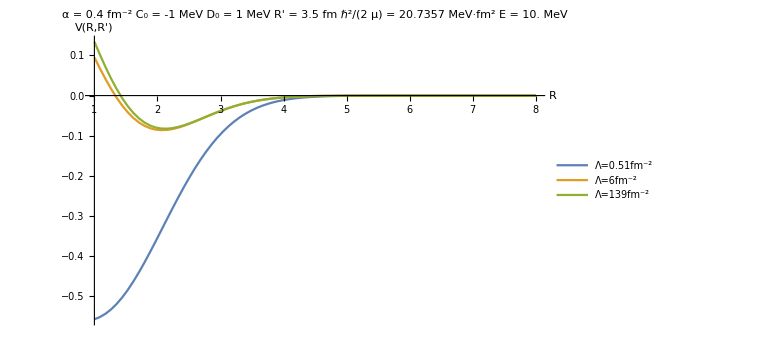

```mathematica
ℏc=197.32858;Mnucl=(938.2796+939.5731)/2.;
mu=Mnucl Z[[1]] Z[[2]]/(Z[[1]]+Z[[2]]);
hbc2m=ℏc^2/(2 mu);

Rmax=8.0;y0=3.5;alpha=0.4;c0=-1;d0=1;en=10.0;lambdas={0.51,6,139};
Plot[Evaluate@Table[Vcomplete[r,y0,alpha,lambda,c0,d0,en,hbc2m],{lambda,lambdas}],{r,1,Rmax},PlotPoints->80,MaxRecursion->0,AxesLabel->{"R","V(R,R')"},PlotLegends->Table["Λ="<>ToString[n]<>"fm^-2",{n,lambdas}],PlotRange->Full,ImageSize->Large,PlotLabel->"α = "<>ToString[alpha]<>" fm^-2   C_0 = "<>ToString[c0]<>" MeV    D_0 = "<>ToString[d0]<>" MeV    R' = "<>ToString[y0]<>" fm    ℏ^2/(2  μ) = "<>ToString[hbc2m]<>" MeV·fm^2     E = "<>ToString[en]<>" MeV"]
```

```mathematica
alphs={0.3};
exponent=Function[{r,rp,alpha},Exp[-33 alpha (r^2+rp^2)] Sinh[-6 alpha r rp]];
Animate[Plot3D[exponent[r,rp,alf],{r,0,1},{rp,0,1}],{alf,0.1,1,0.1},AnimationRunning->False]
```

```mathematica
Integrate[4 Pi r^2 ((2 al/(Pi))^(3/4) Exp[-al r^2])^2,{r,0,Infinity}]
```

ConditionalExpression[1,Re[al]>0]

```mathematica
Integrate[r^4 Exp[-2 al r^2],{r,0,Infinity}]
```

ConditionalExpression[(3 √(π/2))/(32 al^(5/2)),Re[al]>0]

```mathematica
Erf[Infinity]
```

1